# Phase detection over {secrets, interactions}.

## Editing

Feel free to edit this notebook. Please do contribute whatever code or ideas come to mind.

Remember to do Delete All Output before you commit your changes to this file.

## Implementation

### The TSS format

One file containing multiple time series. Like multiple .csv files in one file, separated by blank lines. Plus a leading “SECRET:____” line. That’s it.

## Parse a TSS file

Parse TSS file and return {secrets, interactions} — a list of strings and a list of Datasets.

```mathematica
ParseTssFile[pathname_]:=Module[{text,chunklist,tuples,secrets,interactions},
text=Import[pathname, "Text"];
chunklist=StringSplit[text,"\n\n"];
tuples=ParseTssChunk/@chunklist;
secrets=First/@tuples;
interactions=Last/@tuples;
Print@DescribeSecsIAs[secrets,interactions];
{secrets,interactions}
]
```

#### Hack: Caching version of ParseTssFile

This uses the global variable tssCache (an Association) as a cache from TSS file names to {secs, ias} pairs.
Warning, this could use up a lot of memory!

```mathematica
ParseTssFileCaching[pathname_]:=Module[{text,chunklist,tuples,secrets,interactions},
(* Create an empty cache if it doesn't exist yet. *)
If[Not@AssociationQ[tssCache],tssCache=Association[]];
(* Have we already parsed this filename? *)
If[KeyExistsQ[tssCache,pathname],
{secrets,interactions}=tssCache[[pathname]];Print@DescribeSecsIAs[secrets,interactions];,
(* else *)
{secrets,interactions}=ParseTssFile[pathname];AssociateTo[tssCache,pathname->{secrets,interactions}];
];
Return[{secrets,interactions}];
]

ClearTssCache[]:=Clear[tssCache];
```

#### Parse one chunk of a TSS file.

The first line contains SECRET: followed by the secret.
The second line contains comma-separated column labels.
The rest of the lines contain comma-separated values.

```mathematica
ParseTssChunk[chunk_]:=Module[{secretline, headerline, restcsv, secret,columnnames,matrix,packets},
{secretline, headerline,restcsv}=StringSplit[chunk, "\n",3];
secret=Last@StringSplit[secretline,"SECRET:",2];
columnnames=StringSplit[headerline,","];
matrix=ImportString[restcsv,"CSV"];
packets=Dataset[AssociationThread[columnnames,#]&/@matrix];
<|"secret"->secret,"packets"->packets|>
]
```

#### Describe a {secrets, interactions} pair.

```mathematica
DescribeSecsIAs[secs_,ias_]:=Column[{
"Interactions"->Length[ias],
"Secrets"->Length[secs],
"Unique secrets"->Length[DeleteDuplicates[secs]],
"Min time"->MinTimeInIAs[ias],
"Max time"->MaxTimeInIAs[ias]
}]
```

## Show secrets

```mathematica
ShowSecrets[secs_]:=Dataset[Map[<|{"secret"->#}|>&,secs]]
ShowUniqueSecrets[secs_]:=ShowSecrets[DeleteDuplicates[secs]]
```

## Separate interactions by secret value

Given a list of secrets and a list of interactions, return an association secret → list of interactions.

```mathematica
SeparateBySecret[secs_,ias_]:=Module[{posindex},
posindex=PositionIndex[secs];
Map[ias[[#]]&,posindex]
]
```

## Convert interaction to EventSeries

Just size over time. EventSeries are useful because of Mathematica built-in functions on them.

```mathematica
IA2ES[ia_]:=EventSeries[Transpose@{Normal@ia[[All,"time"]],Normal@ia[[All,"size"]]}]
```

## Shorthands to get an interaction’s time vector or size vector

```mathematica
TimesIA[ia_]:=Normal[ia[[All,"time"]]]
SizesIA[ia_]:=Normal[ia[[All,"size"]]]
```

## Merge fully-loaded-packet streaks

Given a list of sizes and a maximum payload size M, return another list of sizes where any run of n adjacent appearances of M that is followed by another number A gets replaced by (n×M+A). PEND: Currently, a run of Ms is not replaced if it isn’t followed by something else. Is this correct?

```mathematica
SizesMergedIA[ia_]:=MergeFullyLoadedPacketSizes[SizesIA[ia],1448]

MergeFullyLoadedPacketSizes[sizes_,maxsize_]:=Fold[
Function[{l1,l2},If[Length[l1]>0∧Last[l1]==maxsize,
With[{split=SplitBy[l1,#==maxsize&]},
Join[
Catenate[Drop[split,-1]],
{Total[Join[Last[split],Take[l2,1]]]},
Drop[l2,1]
]
],
Join[l1,l2]
]
],
{},
SplitBy[sizes,#==maxsize&]
]
```

```mathematica
MergeFullyLoadedPacketSizes[{14,11,0,0,15,1448,45,198,6,1448,1448,1448,141,15,1448,2,37,298,341},1448]
```

{14,11,0,0,15,1493,198,6,4485,15,1450,37,298,341}

This version returns another interaction with the streaks merged. This is useful as it allows us to apply IA functions (like ShowIA, BubbleChartIAs, etc) to the aggregated version of the interaction.

NOTE: Flags, src/dst IP & ports, etcetera are those of the FIRST packet of the streak. This is not exactly “true”, but will do for now.
PEND: We currently DO NOT check that the whole streak is going in the same direction. We make the decision based solely on packet sizes. Beware!

```mathematica
MergeStreaksIA[ia_,magicSize_]:=Module[{
result={},
currPos=1,
currSize,totalSize,
streakLength=0,
streakFirstEvent,superPacket
},
While[currPos≤Length[ia],
	currSize=ia[[currPos]]["size"];
	If[currSize==magicSize,
	(* found a magic elem *)
		If[streakLength==0,
		(* then: it's the first of a streak, save its info *)
			streakFirstEvent=ia[[currPos]];
			streakLength++,
		(* else: it's not the first of a streak *)
			streakLength++;
		],
	(* else: found a nonmagic elem *)
		If[streakLength>0,
		(* then: it's the first nonmagic after a streak *)
			totalSize=streakLength*magicSize+currSize;
			superPacket=Normal@ReplacePart[streakFirstEvent,"size"->totalSize];
			AppendTo[result,superPacket];
			streakLength=0,
		(* else: it's just a normal nonmagic *)
			AppendTo[result,Normal@ia[[currPos]]];
		];
	];
	currPos++;
];
Dataset[result]
]

(* default magic size *)
MergeStreaksIA[ia_]:=MergeStreaksIA[ia,1448]
```

## Filter markers from an interaction

Test whether a row of an interaction is a marker.

```mathematica
MarkerQ[iaRow_]:=iaRow[["sport"]]==iaRow[["dport"]]==55555
NonMarkerQ[iaRow_]:=¬MarkerQ[iaRow]
```

Select the rows that are markers.

```mathematica
MarkersIA[ia_]:=ia[Select[MarkerQ]]
```

Select the rows that aren’t markers.

```mathematica
RemoveMarkersIA[ia_]:=ia[Select[NonMarkerQ]]
```

## Separate an interaction by {src,dst} IP address pair

Calculate the list of unique {src,dst} pairs in an interaction.

```mathematica
SrcDstPairsInIA[ia_]:=DeleteDuplicates[ia[All,{#src,#dst}&]]
```

Given an interaction, return a list of interactions, each of which only contains events with a particular value of {src,dst}.

```mathematica
SeparateBySrcDst[ia_]:=Module[{srcdstpairs},
srcdstpairs=SrcDstPairsInIA[ia];
Table[
ia[Select[Normal@{#src,#dst}==Normal@srcdstpairs[[i]]&]],{i,1,Length@srcdstpairs}
]
]
```

PEND: need to improve this to consider port numbers as well.
Not fully trivial because source ports are arbitrary and they keep changing.
Probably best to specify which ports are well-known for the experiment, and treat all other ports as the same thing.

### Visualizations colored by {src,dst}

Given an interaction, return N lists of times, where N is the number of distinct {src,dst} pairs in the interaction.
In each list, the times that do not correspond to that {src,dst} are replaced by None.

```mathematica
TimesSrcDstIA[ia_]:=Module[{srcdstpairs,timesrcdst},
srcdstpairs=Normal[SrcDstPairsInIA[ia]];
timesrcdst=Normal[
Map[
{#time,{#src,#dst}}&,
ia[[All,{"time","src","dst"}]]
]
];
Table[
Table[
If[timesrcdst[[j]][[2]]==srcdstpairs[[i]],
timesrcdst[[j]][[1]],
None],
{j,1,Length@timesrcdst}
],
{i,1,Length@srcdstpairs}
]
]
```

Analogous to the above, but size-only instead of time-only.

```mathematica
SizesSrcDstIA[ia_]:=Module[{srcdstpairs,sizesrcdst},
srcdstpairs=Normal[SrcDstPairsInIA[ia]];
sizesrcdst=Normal[
Map[
{#size,{#src,#dst}}&,
ia[[All,{"size","src","dst"}]]
]
];
Table[
Table[
If[sizesrcdst[[j]][[2]]==srcdstpairs[[i]],
sizesrcdst[[j]][[1]],
None],
{j,1,Length@sizesrcdst}
],
{i,1,Length@srcdstpairs}
]
]
```

```mathematica
ShowTimesSrcDstIA[ia_]:=ShowTimesSrcDstIA[ia,{}]
ShowTimesSrcDstIA[ia_,args__]:=ListPlot[TimesSrcDstIA[ia],args]

ShowSizesSrcDstIA[ia_]:=ShowSizesSrcDstIA[ia,{}]
ShowSizesSrcDstIA[ia_,args__]:=ListPlot[SizesSrcDstIA[ia],args]
```

## Show an interaction

Visualize a single interaction. Triple view: event series, size-only, time-only.

NEW: We now show different colors for each {src,dst} pair.

```mathematica
ShowIA[ia_]:=ShowIA[ia,{}]
ShowIA[ia_,args__]:=Module[{es=IA2ES@ia},
TabView[{
"Size over time"->ListPlot[IA2ES/@SeparateBySrcDst[ia],
args,
AxesLabel->{"Time","Packet size"},Filling->Axis,ImageSize->Full,LabelStyle->14],
"Size only"->ShowSizesSrcDstIA[ia,
args,
AxesLabel->{"Packet index","Packet size"},Filling->Axis,ImageSize->Full,LabelStyle->14],
"Time only"->ShowTimesSrcDstIA[ia,
args,
AxesLabel->{"Packet index","Packet time"},ImageSize->Full,LabelStyle->14]
}]
]
```

## Show many interactions

Visualize a list of interactions, superimposed together.

```mathematica
ShowIAs[ias_]:=Module[{ess=IA2ES/@ias},
TabView[{
"Size over time"->ListPlot[ess,ImageSize->Full,AxesLabel->{"Time","Packet size"}],
"Size only"->ListPlot[#["Values"]&/@ess,ImageSize->Full,AxesLabel->{"Packet index","Packet size"}],
"Time only"->ListPlot[#["Times"]&/@ess,ImageSize->Full,AxesLabel->{"Packet index","Packet time"}]
}]
]
```

## Aggregate functions over lists of interactions

Maximum and minimum size and time over many interactions.

```mathematica
MinTimeInIAs[ias_]:=Min[Map[#[Min,"time"]&,ias]];
MaxTimeInIAs[ias_]:=Max[Map[#[Max,"time"]&,ias]];

MinSizeInIAs[ias_]:=Min[Map[#[Min,"size"]&,ias]];MaxSizeInIAs[ias_]:=Max[Map[#[Max,"size"]&,ias]];
```

## Extract a sub-interaction (time window)

Extract the sub-interaction within a time window.

```mathematica
TimeWindowIA[ia_,range_]:=ia[Select[First[range]≤#time≤Last[range]&]]
TimeWindowIAs[ias_, range_]:=Map[TimeWindowIA[#,range]&,ias]
```

## Browse list of interactions

Browse through multiple interactions using a slider. Slow with too many ias. Try a smaller RandomSample of your interactions first.

PEND: Rethink the scaling issue. Max? Auto?

```mathematica
BrowseSizeIAs[ias_]:=With[{},
Manipulate[
Column[{
ShowSizesSrcDstIA[ias[[j]],
ImageSize->Large,
Filling->Bottom
],
"Interaction "<>ToString@j<>" of "<>ToString@Length@ias
}],
{j,1,Length[ias],1}
]
]
```

```mathematica
BrowseTimeIAs[ias_]:=With[{},
Manipulate[
Column[{
ShowTimesSrcDstIA[ias[[j]],
(*PlotRange->{0,maxt},*)
ImageSize->Large,
Filling->Bottom
],
"Interaction "<>ToString@j<>" of "<>ToString@Length@ias
}],
{j,1,Length[ias],1}
]
]
```

This is a slightly older version.

```mathematica
BrowseIAs[interactions_]:=With[{
maxtime=MaxTimeInIAs[interactions],
maxsize=MaxSizeInIAs[interactions]
},
Manipulate[
Column[{
ListPlot[
Map[IA2ES,SeparateBySrcDst[ interactions[[j]] ]],
PlotRange->{{0,maxtime},{0,maxsize}},
ImageSize->Large,
Filling->Bottom
],
"Interaction "<>ToString@j<>" of "<>ToString@Length@ias
}],
{j,1,Length[ias],1}
]
]
```

## Manually align interactions by interactive shifting

Given two interactions and a {lo,hi} range, match them by shifting one of them by moving a slider.

PEND: The default range should be {-1,1}.

```mathematica
ManuallyAlignIAs[ia1_,ia2_,range_]:=Module[
{},
Manipulate[
Column[{
ListPlot[ 
{TimeSeriesShift[IA2ES@ia1,delta],IA2ES@ia2} ,
ImageSize->Large,
Filling->Bottom
],
delta
}],
{delta,First@range,Last@range}
]
]
```

```mathematica
ManuallyAlignIAsWithMinimizeButton[ia1_,ia2_,range_]:=Module[
{},
Manipulate[
Column[{
ListPlot[ 
{TimeSeriesShift[IA2ES@ia1,delta],IA2ES@ia2} ,
ImageSize->Large,
Filling->Bottom
],
delta
}],
{delta,First@range,Last@range},
Button["Foo!",delta=Last@First@Last[MinimizeWarpingDistanceIAs[ia1,ia2]]]
]
]
```

## Align interactions by an offset that minimizes time-warping distance

This shows where the minimum is.

PEND: It would be nice to compute this. Minimize and NMinimize can do it, but both raise warnings.
 
PEND: The choice of 100 is arbitrary; use something more robust.

PEND: Could reuse aux func below instead of building an EventSeries.

```mathematica
ShowWarpingDistanceIAs[ia1_,ia2_,range_]:=Module[{es1=IA2ES@ia1,es2=IA2ES@ia2},
DiscretePlot[
WarpingDistance[
Normal@TimeSeriesShift[es1,δ],
Normal@es2
],
{δ,First@range,Last@range,(Last@range-First@range)/100},
ImageSize->Large
]
]
```

```mathematica
WarpingDistanceTimeIAs[ia1_,ia2_]:=WarpingDistance[TimesIA[ia1],TimesIA[ia2]]
```

NEW: Minimization without warnings!
Chop will replace near-zero with zero if smaller than 10^-10.

```mathematica
MinimizeWarpingDistanceIAs[ia1_,ia2_]:=
Chop@NMinimize[
Hold[
WarpingDistance[
TimesIA[ ia1 ]+δ,
TimesIA[ ia2 ]
]
],
δ
]
```

## Align interactions based on the first packet before/after a certain point

This is useful to horizontally align a part of the interaction, whenever we are willing to assume that it can safely be aligned. 

Of course, this distorts the data. Only use this when you are fairly certain that the distortion is innocuous.

### Left-alignment: move events that take place after a given point.

Given an interaction, an alignment point in time A and a target point in time T, return a new interaction where all events that occurred after A are shifted by a constant, such that the first post-A event now occurs at T (and the rest of the post-A events are shifted by the same amount).

```mathematica
AlignLeftFromAtIA[ia_,from_,at_]:=Module[{firstAfterFrom,timeFirstAfterFrom,shift},
firstAfterFrom=ia[SelectFirst[#time>from&]];
timeFirstAfterFrom=If[MissingQ[firstAfterFrom],firstAfterFrom,firstAfterFrom["time"]];
shift=If[MissingQ[firstAfterFrom],0.0,(at-timeFirstAfterFrom)];
ia[All,{"time"->(If[#≥timeFirstAfterFrom,#+shift,#]&)}]
]
```

Generalization to list of interactions.

```mathematica
AlignLeftFromAtIAs[ias_,from_,at_]:=Map[AlignLeftFromAtIA[#,from,at]&,ias]
```

### Right-alignment: move events that take place before a given point.

Alternatively, one can align right. In that case, all events that occurred before A are shifted so that the first pre-A event now occurs at T (and the rest of the pre-A events are shifted by the same amount).

```mathematica
AlignRightFromAtIA[ia_,from_,at_]:=Module[{rowsBeforeFrom,firstBeforeFrom,timeFirstBeforeFrom,shift},
rowsBeforeFrom=ia[Select[#time<from&]];
firstBeforeFrom=If[Length[rowsBeforeFrom]>0,Last@rowsBeforeFrom,Nothing];
timeFirstBeforeFrom=If[Length[rowsBeforeFrom]>0,firstBeforeFrom["time"],firstBeforeFrom];
shift=If[Length[rowsBeforeFrom]>0,(at-timeFirstBeforeFrom),0.0];
ia[All,{"time"->(If[#≤timeFirstBeforeFrom,#+shift,#]&)}]
]
```

Generalization to list of interactions.

```mathematica
AlignRightFromAtIAs[ias_,from_,at_]:=Map[AlignRightFromAtIA[#,from,at]&,ias]
```

### Default is to align left.

```mathematica
AlignFromAtIA=AlignLeftFromAtIA;
AlignFromAtIAs=AlignLeftFromAtIAs;
```

PEND: These function names suck. Any better ideas?
PEND: The left/right choice could be implemented as an Option, rather than separate functions.

## Shift an interaction by a certain amount of time

Add/subtract a constant offset to all times.

```mathematica
ShiftIA[ia_,offset_]:=ia[All,{"time"->(#+offset&)}]
```

## Canonical time warping correspondence

This is another way to find similarity-zones over time between two interactions.

PEND: Generalize to N interactions!

```mathematica
CanonicalWarpingCorrespondenceTimeIAs[ia1_,ia2_]:=CanonicalWarpingCorrespondence[TimesIA[ia1],TimesIA[ia2]]
```

```mathematica
CanonicalWarpingCorrespondenceSizeIAs[ia1_,ia2_]:=CanonicalWarpingCorrespondence[SizesIA[ia1],SizesIA[ia2]]
```

```mathematica
CanonicalWarpingCorrespondenceTimeAndSizeIAs[ia1_,ia2_]:=CanonicalWarpingCorrespondence[Normal@IA2ES[ia1],Normal@IA2ES[ia2]]
```

```mathematica
ShowCanonicalWarpingCorrespondenceIAs[ia1_,ia2_]:=Module[{path,z},
path=Transpose@CanonicalWarpingCorrespondenceIAs[ia1,ia2];
z=WhereIsStraightPath[path];
ListPlot[{path,path},ImageSize->Medium,AspectRatio->1]
]
```

This returns one Boolean per gap between datapoints.

```mathematica
WhereIsStraightPath[path_]:=Join[{1},
Table[
If[path[[i-1]]+{1,1}==path[[i]],
1,
0
],
{i,2,Length[path]}
]
]
```

## Bubble chart for a list of interactions

### Aux function

This generates a list of {time, y, size} tuples, where y is the number (index) of the interaction.

```mathematica
IAs2BubbleTriplets[interactions_]:=Module[{ess,listsofpairs},
listsofpairs=Normal/@IA2ES/@interactions;
Table[
Table[{
listsofpairs[[i]][[j]][[1]],
i,
listsofpairs[[i]][[j]][[2]]
},
{j,1,Length@listsofpairs[[i]]}],
{i,1,Length@listsofpairs}
]
]
```

### Plot the bubble chart

This can get slow for >50 interactions. Try a smaller RandomSample first.
Using PerformanceGoal → Speed makes the chart non-interactive, but is faster and uses less memory.

```mathematica
BubbleChartIAs[interactions_,otherargs__]:=BubbleChart[
IAs2BubbleTriplets[interactions],
otherargs,ImageSize->Full, BubbleSizes->Small,PerformanceGoal->"Speed"
]

BubbleChartIAs[interactions_]:=BubbleChartIAs[interactions,{}]
```

## Interaction to free-time and busy-time intervals

Interval object with the union of all the packet-free intervals.
packetradius is the radius of the “non-free” zone created by each packet.
NOTE: This does not include the endpoints {-∞, 0-packetradius} and {lastpkt+packetradius, +∞}
NOTE: We filter out any subintervals {a,b} with a > b, as Interval interprets them as {b,a} rather than discarding them (!)

```mathematica
IA2FreeInterval[interaction_,packetradius_]:=Module[{
times=Normal[interaction[[All,"time"]]],
pairs,
filteredpairs
},
pairs=Transpose[ {
Drop[times+packetradius,-1],
Drop[times-packetradius,1]
} ];
filteredpairs=Select[pairs,#[[1]]<#[[2]]&];
Interval@@filteredpairs
]
```

Same thing, but now keeping track of busy intervals instead of free intervals.

```mathematica
IA2BusyInterval[interaction_,packetradius_]:=Module[{
times=Normal[interaction[[All,"time"]]],
lefts,rights,pairs,filteredpairs
},
lefts=Clip[times-packetradius,{0,∞}];
rights=times+packetradius;
pairs=Transpose@{lefts,rights};
filteredpairs=Select[pairs,#[[1]]<#[[2]]&];
Interval@@filteredpairs
]
```

## Filter interactions to get only events that lie inside/outside an Interval

```mathematica
SelectInsideIntervalIA[ia_,iv_]:=ia[Select[IntervalMemberQ[iv,#time]&]]
SelectOutsideIntervalIA[ia_,iv_]:=ia[Select[Not@IntervalMemberQ[iv,#time]&]]

SelectInsideIntervalIAs[ias_,iv_]:=Map[SelectInsideIntervalIA[#,iv]&,ias]
SelectOutsideIntervalIAs[ias_,iv_]:=Map[SelectOutsideIntervalIA[#,iv]&,ias]
```

## Visualize free-time and busy-time intervals

### Show an Interval

```mathematica
ShowInterval[iv_]:=ShowInterval[iv,{}]
ShowInterval[iv_,args__]:=NumberLinePlot[iv,{x,Min@iv,Max@iv},ImageSize->Large]
```

```mathematica
ExplicitSubintervals[iv_]:=Map[Interval,{Sequence@@iv}]
```

### Show an Interval and its composition

```mathematica
ShowIntervalExplicit[iv_]:=NumberLinePlot[ExplicitSubintervals@iv,{x,Min@iv,Max@iv},ImageSize->Large]
```

```mathematica
ShowIntervalBoth[iv_]:=ShowIntervalBoth[iv,{}]
ShowIntervalBoth[iv_,args__]:=Column[{
NumberLinePlot[iv,{x,Min@iv,Max@iv},args,ImageSize->Large],
NumberLinePlot[ExplicitSubintervals@iv,{x,Min@iv,Max@iv},args,ImageSize->Large]
}]
```

### Show free-time or busy-time of an interaction

This also shows the “explicit” view with the decomposition of the Interval.

```mathematica
ShowFreeTimeIA[ia_,radiusrange_]:=
Manipulate[
Column[{
ShowIntervalBoth[ IA2FreeInterval[ia,radius] ],
radius
}],
{radius,First@radiusrange,Last@radiusrange}
]
```

```mathematica
ShowBusyTimeIA[ia_,radiusrange_]:=
Manipulate[
Column[{
ShowIntervalBoth[ IA2BusyInterval[ia,radius] ],
radius
}],
{radius,First@radiusrange,Last@radiusrange}
]
```

### Show an interaction along with its free-time or busy-time

Experimental. For this to make sense, the ListPlot and the NumberLinePlot need to be in sync. For busy time it works quite well.

```mathematica
ShowBusyTimeWithIA[ia_,radiusrange_]:=
Manipulate[
Column[{
ListPlot[Normal@ia[[All,{"time","size"}]],Frame->True,Axes->False,FrameTicks->{Automatic,None},Filling->Bottom,ImageSize->Large,
With[{mi=Min@IA2BusyInterval[ia,radius],ma=Max@IA2BusyInterval[ia,radius]},
PlotRange->{{mi-(mi+ma)/8,ma+(mi+ma)/8},Automatic}]
],
ShowInterval[ IA2BusyInterval[ia,radius],Frame->True,FrameTicks->{Automatic,None},ImageSize->Large],
radius
}],
{radius,First@radiusrange,Last@radiusrange}
]
```

The free-time version is not yet as good: it goes out of sync a bit when the NumberLinePlot starts zooming in.

```mathematica
ShowFreeTimeWithIA[ia_,radiusrange_]:=
Manipulate[
Column[{
ListPlot[Normal@ia[[All,{"time","size"}]],Frame->True,Axes->False,FrameTicks->{Automatic,None},Filling->Bottom,ImageSize->Large,
With[{mi=Min@IA2FreeInterval[ia,radius],ma=Max@IA2FreeInterval[ia,radius]},
PlotRange->{{mi-(mi+ma)/8,ma+(mi+ma)/8},Automatic}]
],
ShowInterval[ IA2FreeInterval[ia,radius],Frame->True,FrameTicks->{Automatic,None},ImageSize->Large],
radius
}],
{radius,First@radiusrange,Last@radiusrange}
]
```

### Show free-time intersection and busy-time union over multiple interactions

```mathematica
ShowFreeTimeIntersectionIAs[ias_,radiusrange_]:=
With[{maxtime=MaxTimeInIAs[ias]},
Manipulate[
Column[{
NumberLinePlot[Map[IA2FreeInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
NumberLinePlot[IntervalIntersection@@Map[IA2FreeInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
radius
}],
{radius,First@radiusrange,Last@radiusrange}
]
]
```

The busy-time version now has an Export to JSON button! :)

```mathematica
ShowBusyTimeUnionIAs[ias_,radiusrange_]:=
With[{maxtime=MaxTimeInIAs[ias],destfilename="/tmp/test.json"},
Manipulate[
Column[{
NumberLinePlot[Map[IA2BusyInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
NumberLinePlot[IntervalUnion@@Map[IA2BusyInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
radius
}],
{radius,First@radiusrange,Last@radiusrange},
Button["Export to JSON",ExportBusyTimeUnionIAs[ias,radius,destfilename]],
Button["Show union interval",Print[ToString[IntervalUnion@@Map[IA2BusyInterval[#,radius]&,ias]]]]
]
]
```

```mathematica
ShowBusyTimeOnlyUnionIAs[ias_,radiusrange_]:=
With[{maxtime=MaxTimeInIAs[ias],destfilename="/tmp/test.json"},
Manipulate[
Column[{
NumberLinePlot[IntervalUnion@@Map[IA2BusyInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
radius
}],
{radius,First@radiusrange,Last@radiusrange},
Button["Export to JSON",ExportBusyTimeUnionIAs[ias,radius,destfilename]]
]
]
```

This is a non-interactive version of the above, for a fixed radius.

```mathematica
DisplayBusyTimeOnlyUnionIAs[ias_,radius_]:=
With[{maxtime=MaxTimeInIAs[ias],destfilename="/tmp/test.json"},
Column[{
NumberLinePlot[IntervalUnion@@Map[IA2BusyInterval[#,radius]&,ias],{x,0,maxtime},ImageSize->Large],
radius,
Button["Export to JSON",ExportBusyTimeUnionIAs[ias,radius,destfilename]]
}]
]
```

This is a non-GUI version of the above.

```mathematica
ExportBusyTimeUnionIAs[ias_,radius_,destfilename_]:=Module[{file,jsonstring},
lastIntervalUnion=IntervalUnion@@Map[IA2BusyInterval[#,radius]&,ias];
file=OpenWrite[destfilename];
jsonstring=IAsIV2JSON[ias,lastIntervalUnion];
WriteString [file,jsonstring];
Close[file];
Print["Exported to "<>destfilename];
]
```

## JSON export (old, based on Interval objects)

(This is sometimes not enough because adjacent intervals in an Interval object get merged together. We need a list of pairs instead.)

Many interactions with the same Interval object

```mathematica
IAsIV2JSON[ias_,iv_]:=With[{pairs=Table[{i,f[ias[[i]],iv]},{i,1,Length[ias]}]},
ExportString[
Map[<|"interaction_num"->First[#]-1,"interval_list"->Last@#|>&,pairs],
"RawJSON","Compact"->2
]
]

IAsIV2JSON[ias_,iv_,goodpositions_]:=With[{pairs=Table[{i,f[ias[[i]],iv]},{i,goodpositions}]},
ExportString[
Map[<|"interaction_num"->First[#]-1,"interval_list"->Last@#|>&,pairs],
"RawJSON","Compact"->2
]
]

f[ia_,iv_]:=With[{listOfListsOfIdx=SelectTimeIdxsIA[ia,iv]},
Map[If[Length[#]>0,FirstAndLast[#],{1,0}]&,listOfListsOfIdx]
]

FirstAndLast[elems_]:={First@elems,Last@elems}
```

Many interactions, each with its own Interval object

```mathematica
IAsIVs2JSON[ias_,ivs_]:=With[{pairs=Table[{i,f[ias[[i]],ivs[[i]]]},{i,1,Length[ias]}]},
ExportString[
Map[<|"interaction_num"->First[#]-1,"interval_list"->Last@#|>&,pairs],
"RawJSON","Compact"->2
]
]
```

Input: an interaction and an Interval object.
Output: a list of lists of idxs (original-pcap indices), each with only those events that correspond to the associated sub-interval of the interaction.

```mathematica
SelectTimeIdxsIA[ia_,iv_]:=Map[ Normal[#[[All,"idx"]]]&, SelectIntervalIA[ia,iv] ]

SelectIntervalIA[ia_,iv_]:=Table[
ia[Select[
First[iv[[i]]]≤#time≤Last[iv[[i]]]&
]],
{i,1,Length@iv}
]
```

## Take uniform random sample from all secrets

Take a random sample of N interactions from each secret. Flatten them into one list of interactions.

```mathematica
RandomSampleFromEachSecret[sec2ias_,npersecret_]:=Catenate@Values@Map[RandomSample[#,npersecret]&,sec2ias]
```

## Outlier detection and pruning

Given ias and n, return a list {indices, interactions} of those whose last-packet time is over n standard deviations apart from the mean last-packet time.
Note that the returned indices are wrt to the given ias (not to anything global).

```mathematica
GuessOutliersByLastPacketTimeIAs[ias_,numberOfStdDevs_]:=
Module[{lastpackettimes,mean,stddev,threshold,positions},
lastpackettimes=Map[#[Max,"time"]&,ias];
mean=Mean[lastpackettimes];
stddev=StandardDeviation[lastpackettimes];
threshold=mean+numberOfStdDevs*stddev;
positions=Position[ias,_?(#[Max,"time"]>threshold&)];
{Flatten[positions],Extract[ias,positions],Delete[Range[Length[ias]],positions],Delete[ias,positions]}
]
```

```mathematica
ShowOutliersByLastPacketTimeForIncreasingThresholdIAs[ias_]:=
DiscretePlot[Length[First[GuessOutliersByLastPacketTimeIAs[ias,nstddevs]]],{nstddevs,2,3,0.2}]
```

## Pending

Export certain intervals to JSON that don’t come from a radius-based union calculation.

Number of busy interval segments resulting from a certain radius:

```mathematica
HowManySegmentsBusyIntervalIA[ia_,radius_]:=Length@IA2BusyInterval[ia,radius]
```

```mathematica
ShowHowManySegmentsBusyIntervalsIAs[ias_,radiusrange_]:=Plot[
Map[HowManySegmentsBusyIntervalIA[#,r]&,ias],
{r,First@radiusrange,Last@radiusrange}
]
```

Given an interaction and a desired number of segments (how many intervals in the resulting Interval object), use binary search to find a radius that yields exactly that number of segments. Return the radius and the Interval object.

```mathematica
IA2BusyIntervalWithFixedNumberOfSegments[ia_,desiredNumberOfSegments_]:=Module[{
left=0.000001,
right=ia[Max,"time"]-ia[Min,"time"],
radius,numberOfSegments
},
While[True,
radius=(left+right)/2;
numberOfSegments=HowManySegmentsBusyIntervalIA[ia,radius];
If[numberOfSegments==desiredNumberOfSegments,Break[]];
If[numberOfSegments < desiredNumberOfSegments,right=radius,left=radius];
];
Return[{radius,IA2BusyInterval[ia,radius]}]
]
```

```mathematica
IAs2BusyIntervalsWithFixedNumberOfSegments[ias_,desiredNumberOfSegments_]:=Map[IA2BusyIntervalWithFixedNumberOfSegments[#,desiredNumberOfSegments]&,ias]
```

```mathematica
ShowIAIV[ia_,iv_]:=ListPlot[
Table[
IA2ES@TimeWindowIA[ia,iv[[j]]],{j,1,Length[iv]}
]
]
```

Split an interaction into many by markers. Each of the resulting interactions starts with a marker.

```mathematica
SplitByMarkersIA[ia_]:=Map[Dataset,Split[Normal[ia],Lookup[#2,"flags"]≠"M"&]]
```

Longest common subsequence among N lists.

```mathematica
LCSN[seqs_]:=Fold[LongestCommonSubsequence,seqs[[1]],seqs]
```

This could be more efficient, but I can’t find the right function (that only cares about whether there is at least one appearance). So this will work for now.

```mathematica
IsSublistQ[sublist_,list_]:=Length[SequencePosition[list,sublist]]>0
```

```mathematica
HowManyContainSublist[sublist_,listOfLists_]:=Length[
Select[
listOfLists,
IsSublistQ[sublist,#]&
]
]
```

Assuming sublist is contained within list, return {before, sublist, after} such that their concatenation is list. If there are multiple appearances of sublist within list, the first one is used.

```mathematica
SplitBySublist[list_,sublist_]:=Module[{positionpairs,pStart,pEnd,before,after},
positionpairs=SequencePosition[list,sublist];
{pStart,pEnd}=First[positionpairs];
before=If[pStart>1,Take[list,pStart-1],{}];
after=If[pEnd<Length[list],Take[list,-(Length[list]-pEnd)],{}];
Return[{before,sublist,after}];
]
```

Generate some interesting candidates. LCSN is run on a random subset of the interactions. This is repeated a number of times, and then duplicates are deleted.

```mathematica
LCSNCandidates[ias_]:=Module[{iasizes,significantFraction=0.1,significantNumber,howManyTries=20},
iasizes=Map[SizesIA,ias];
significantNumber=significantFraction * Length[iasizes];
DeleteDuplicates[Table[LCSN[RandomChoice[iasizes,significantNumber]],howManyTries]]
]
```

Look at a bunch of interactions and try to gain insight from the size sequences.

```mathematica
LCSNStudySizes[ias_]:=Module[{iasizes},
iasizes=SizesIA/@ias;
Print["Length frequencies: "<>ToString[Tally[Length/@iasizes]]];
Print["Longest sublist common to all: "<>ToString[LCSN[iasizes]]]
]
```

Return all (maximally non-overlapping) common subsequences with at least the given number of elements.

```mathematica
AllCommonSubsequencesWithLengthAtLeast[list1_,list2_,minLength_]:=Module[{
length1=Length@list1,
length2=Length@list2,
lcs,lcsPos,before1,dummy1,after1,before2,dummy2,after2
},
If[length1<minLength∨length2<minLength,
Return[{}],
lcs=LongestCommonSubsequence[list1,list2];
If[Length[lcs]<minLength,
Return[{}],
{before1,dummy1,after1}=SplitBySublist[list1,lcs];
{before2,dummy2,after2}=SplitBySublist[list2,lcs];
Return[
Join[
{lcs},
AllCommonSubsequencesWithLengthAtLeast[before1,before2,minLength],
AllCommonSubsequencesWithLengthAtLeast[after1,after2,minLength]
]
]
]
]
]
```

Given a list and a number (typically 1448), return a list of lists that don’t contain anything greater than that number, which, if concatenated together, would yield a list equal to the original list after deletion of all elements greater than the given number. For example, SplitListByAnyNumberGreaterThan[{8, 7, 300, 5, 6, 7, 100, 8, 9, 200}] returns {{8, 7}, {5, 6, 7}, {8, 9}}.
PEND: Should we be using 1448 or 1447 here? In other words, < or ≤ ? Remember to double-check, as that could be nontrivial.

```mathematica
SplitListByAnyNumberGreaterThan[list_,n_]:=
Select[
Map[
Select[#,(#≤n&)]&,
Split[list,#≤n&]
],
Length[#]>0&
]
```

This is an attempt to find common (adjacent) subsequences of at least a certain length between two lists of packet sizes.
First, sizes are merged whenever streaks of 1448 are found (see SizesMergedIA).
Then we find all common subsequences of at least minLength elements using a recursive algorithm.
Then we split those whenever a greater-than-1448 super-element is encountered, removing such elements and any empty lists generated.
Then we flatten the result at level 1 so that a list of sublists is returned.
Finally, we filter by minLength again, since the final sublists could indeed be shorter than that.

PEND: This is far from perfect. It’s by no means a guaranteed-exhaustive result, but can be interesting as a way to generate some candidates.

```mathematica
FindCommonSizeSubsequencesAttempt1[ia1_,ia2_,minLength_]:=
Select[
Flatten[
Map[
SplitListByAnyNumberGreaterThan[#,1448]&,
AllCommonSubsequencesWithLengthAtLeast[SizesMergedIA@ia1,SizesMergedIA@ia2,minLength]
],
1
],
Length[#]≥minLength&
]
```

This is an attempt to generate candidates using the above.
NOTE: We are using SizesMergedIA to search for candidates, but SizesIA for ensuring that they are in almostAll. Should make no difference, right?

PEND: This is sometimes failing to find a good candidate due to the abundance of an even longer candidate. For example, in a dataset from airplan_3, {30,11,0,0,216} appears in 650 of 1000 ias, but {11,0,0,216} (without the 30) appears in all 1000 ias. It’s possible for the random samplings to always pick {30,11,0,0,216}, never pick {11,0,0,216}, and then rule out {30,11,0,0,216} due to being present in too low a fraction of the ias, therefore failing to spot that {11,0,0,216} is in all of them.

PEND: Another more mysterious case: {198,6,53,586,373,37,282,341} appears on 997 of 1000 ias, whereas {6,53,586,373,37,282,341} (without the 198) appears in all 1000 ias. Why do we sometimes get neither, using 0.95 as almostAllFraction??

```mathematica
FindCommonSizeSubsequencesAttempt1Candidates[ias_]:=Module[{almostAllFraction=0.95,almostAll,howManyTries=50,minLength=3,cands,iasizes},
almostAll=almostAllFraction * Length[ias];
cands=DeleteDuplicates[
Flatten[
Table[
FindCommonSizeSubsequencesAttempt1[
Sequence@@Join[RandomSample[ias,2],{minLength}]
],
howManyTries
]
,
1
]
];
iasizes=Map[SizesIA,ias];
Sort@Select[
cands,
HowManyContainSublist[#,iasizes]≥almostAll&
]
]
```

Let’s retry, now using all sublists of minLength within each maximally-long candidate. This could get expensive but shouldn’t miss candidates so often.

```mathematica
AllSubsequencesOfLengthAtLeast[list_,minLength_]:=Subsequences[list,{minLength,∞}]
```

```mathematica
TimesIA[a]
```

{0.,0.0132799148559570313,0.013545989990234375,0.0290470123291015625,0.0412089824676513672,0.0417528152465820313,0.1144328117370605469,0.1144788265228271484,0.1162109375,0.1217830181121826172,0.1229310035705566406,0.1240389347076416016,0.1310138702392578125,0.1393768787384033203,0.1427209377288818359,0.1543538570404052734,0.1574289798736572266,0.1590938568115234375,0.1604938507080078125,0.160493851708007812}

```mathematica
SizesIA[a]
```

{112,0,0,192,778,230,6,85,277,213,69,117,117,117,117,117,437,0,69,0}

```mathematica
SizesIA[b]
```

{108,0,0,192,778,230,6,85,277,213,69,117,117,117,117,117,437,0,69,0}

```mathematica
Riffle[SizesIA[a],TimesIA[a]]
```

{112,0.,0,0.0132799148559570313,0,0.013545989990234375,192,0.0290470123291015625,778,0.0412089824676513672,230,0.0417528152465820313,6,0.1144328117370605469,85,0.1144788265228271484,277,0.1162109375,213,0.1217830181121826172,69,0.1229310035705566406,117,0.1240389347076416016,117,0.1310138702392578125,117,0.1393768787384033203,117,0.1427209377288818359,117,0.1543538570404052734,437,0.1574289798736572266,0,0.1590938568115234375,69,0.1604938507080078125,0,0.160493851708007812}

```mathematica
das=TimesIA[a][[2;;]]-TimesIA[a][[;;-2]]
```

{0.0132799,0.0002660751342773438,0.015501022338867188,0.012161970138549805,0.0005438327789306641,0.0726799964904785156,0.0000460147857666016,0.001732110977172852,0.0055720806121826172,0.001147985458374023,0.001107931137084961,0.0069749355316162109,0.0083630084991455078,0.0033440589904785156,0.011632919311523438,0.0030751228332519531,0.001664876937866211,0.001399993896484375,9.999999995×10^-10}

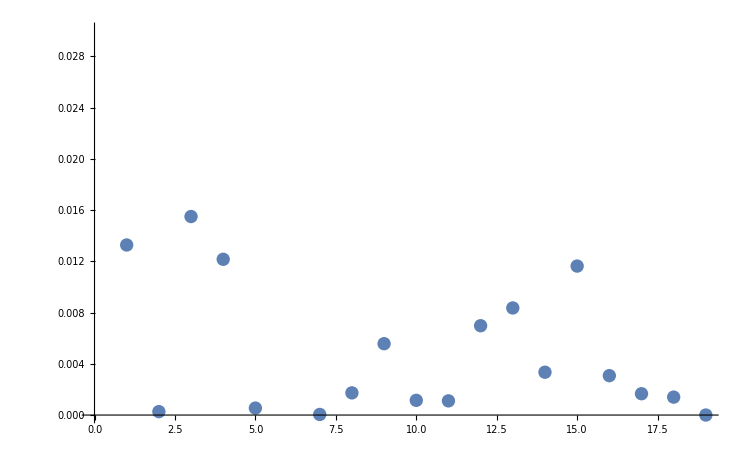

{0.,0.0132799148559570313,0.013545989990234375,0.0290470123291015625,0.0412089824676513672,0.0417528152465820313,0.1144328117370605469,0.1144788265228271484,0.1162109375,0.1217830181121826172,0.1229310035705566406,0.1240389347076416016,0.1310138702392578125,0.1393768787384033203,0.1427209377288818359,0.1543538570404052734,0.1574289798736572266,0.1590938568115234375,0.1604938507080078125}

```mathematica
ListPlot[das]
```

```mathematica
Quantas[ia_,multipleOf_]:=ia[All,{"time"->(Round[#,multipleOf]&)}]
```

Given an interaction, return a Ri starting with Size where the sizes are interleaved with the deltas between packets.

```mathematica
IA2Ri[ia_]:=With[{times=TimesIA[ia],sizes=SizesIA[ia]},
Ri[
Size,
Riffle[
sizes,
Drop[times,1]-Drop[times,-1]
]
]
]
```

```mathematica
TryAlign[ia1_,ia2_,distfun_]:=Module[{s1,s2,plot1,plot2,plot3,plot4,wis,imgsize},
{s1,s2}=SizesIA/@{ia1,ia2};
maxn=Max[Length/@{s1,s2}];
imgsize=Medium;
plot1=ListPlot[s1,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
plot2=ListPlot[s2,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
{p1,p2}=WarpingCorrespondence[s1,s2,DistanceFunction->distfun];
plot3=ListPlot[Transpose@{p1,p2},ImageSize->imgsize];
arrayplot=ArrayPlot@{WhereIsStraightPath[Transpose@{p1,p2}]};
plot4=ListPlot[Transpose@{s1[[p1]],s2[[p2]]},ImageSize->imgsize];
Column[{plot1,plot2,plot3,arrayplot,plot4}]
]

TryAlign[ia1_,ia2_]:=TryAlign[ia1,ia2,Automatic]
```

```mathematica
ShowDiagonalZones[ias_]:=Module[{ss,warpz,plotz,imgsize,npairs},
ss=SizesMergedIA/@ias;
imgsize=Medium;
npairs=70;
warpz=Map[WarpingCorrespondence[First@#,Last@#]&,
Table[RandomSample[ss,2],{i,1,npairs}]
];
plotz=Column[
Table[
ArrayPlot[{WhereIsStraightPath[Transpose@warpz[[j]]]},ImageSize->imgsize,Frame->None,ImagePadding->None,Mesh->All,PlotRangePadding->0],
{j,1,Length@warpz}
]
];
plotz
]
```

```mathematica
TryAlign[ia1_,ia2_]:=Module[{s1,s2,plot1,plot2,plot3,plot4,wis,imgsize,arrayplot,maxn},
{s1,s2}=SizesIA/@{ia1,ia2};
maxn=Max[Length/@{s1,s2}];
imgsize=Medium;
plot1=ListPlot[s1,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
plot2=ListPlot[s2,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
{p1,p2}=WarpingCorrespondence[s1,s2];
plot3=ListPlot[Transpose@{p1,p2},ImageSize->imgsize];
arrayplot=ArrayPlot@{WhereIsStraightPath[Transpose@{p1,p2}]};
plot4=ListPlot[Transpose@{s1[[p1]],s2[[p2]]},ImageSize->imgsize];
Column[{plot1,plot2,plot3,arrayplot,plot4}]
]
```

```mathematica
TryAlignMerged[ia1_,ia2_]:=Module[{s1,s2,plot1,plot2,plot3,plot4,wis,imgsize,arrayplot,maxn},
{s1,s2}=SizesMergedIA/@{ia1,ia2};
Print[s1-s2];
maxn=Max[Length/@{s1,s2}];
imgsize=Medium;
plot1=ListPlot[s1,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
plot2=ListPlot[s2,PlotRange->{{1,maxn},Automatic},ImageSize->imgsize];
{p1,p2}=WarpingCorrespondence[s1,s2];
Print[p1-p2];
plot3=ListPlot[Transpose@{p1,p2},ImageSize->imgsize];
arrayplot=ArrayPlot@{WhereIsStraightPath[Transpose@{p1,p2}]};
plot4=ListPlot[Transpose@{s1[[p1]],s2[[p2]]},ImageSize->imgsize];
Column[{plot1,plot2,plot3,arrayplot,plot4}]
]
```

```mathematica
SubwayCactus[ia_,otherias_]:=Module[{sia,soias},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
Column[{
ListPlot[
Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]],
ImageSize->Large,AspectRatio->1,Joined->True
],
ListPlot[
SizesIA[ia],
ImageSize->Large,AspectRatio->1,Filling->Axis
]
}]
]
```

```mathematica
WhereIsStraightPath[path_]:=Join[{1},
Table[
If[path[[i-1]]+{1,1}==path[[i]],
1,
0
],
{i,2,Length[path]}
]
]
```

The following code is wrong!  It fails to capture the difference between “going up” and “going right”.  Works well for concave paths but fails for convex ones, or vice versa.

```mathematica
Wisper[path_]:=Module[{curr=1,lastDiagStart=1,currInDiag=True,result},
result={};
While[curr<Length[path],
If[path[[curr]]+{1,1}==path[[curr+1]],
(*then*)
	If[Not[currInDiag],
	(*then*)
		currInDiag=True;
		lastDiagStart=curr;
	],
(*else*)
	If[currInDiag,
	(*then*)
		AppendTo[result,{lastDiagStart,curr}];
		lastDiagStart=curr; (*hmmm*)
		currInDiag=False;
	]
];
curr++;
];
Return[result];
]
```

```mathematica
ExpandedWisper[path_]:=Module[{ival,range},
ival=Interval@@Wisper[path];
range=Range[Min[ival],Max[ival]];
Select[range,IntervalMemberQ[ival,#]&]
]
```

```mathematica
ExpandedWisperDense[path_]:=Module[{ival,range},
ival=Interval@@Wisper[path];
range=Range[Min[ival],Max[ival]];
Map[If[IntervalMemberQ[ival,#],1,0]&,range]
]
```

```mathematica
Chu[ia_,otherias_]:=Module[{sia,soias,paths,wisps,ivals},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
wisps=Map[Wisper,paths];
ivals=Map[Interval@@#&,wisps]
]
```

```mathematica
Foo[ia_,otherias_]:=Module[{sia,soias,paths,ewisps},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
ewisps=Map[ExpandedWisper,paths]
]
```

```mathematica
FooDense[ia_,otherias_]:=Module[{sia,soias,paths,ewisps},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
ewisps=Map[ExpandedWisperDense,paths]
]
```

```mathematica
NewWisper[path_]:=Module[{tuples,runs,runlengths,prefixsums,fromtopairs,boolsbetweenpoints},
(*each tuple can either be {1,1}, {1,0}, or {0,1}*)
tuples=Drop[path,1]-Drop[path,-1];
(*split the list in adjacent runs of identical tuples*)
runs=Split[tuples];
(*remove any runs of vertical steps*)
runs=Select[runs,Not[First[#]=={0,1}]&];
(*replace {1,1} with 1 and {1,0} with 0*)
runs=Map[Last,runs,{2}];
runlengths=Map[Length,runs];
(*generate a {from,to} pair for each run*)
(*remember that path elements represent the spaces between datapoints, not the datapoints!*)
prefixsums=FoldList[Plus,1,runlengths];
fromtopairs=Transpose@{Drop[prefixsums,-1],Drop[prefixsums,1]};
boolsbetweenpoints=Flatten[runs];
Return[{fromtopairs,boolsbetweenpoints}];
]
```

```mathematica
NewViz[ia_,otherias_]:=Module[{sia,soias,paths,vectors},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
vectors=Map[Last[NewWisper[#]]&,paths];
Return[vectors];
]
```

```mathematica
Column@Map[
ArrayPlot[{#},Mesh->All,ImageSize->Large,Frame->None,ImagePadding->None]&,
Table[
Total@NewViz[ias[[i]],RandomSample[ias,15]],
{i,1,20}
]
]
```

```mathematica
NewViz2[ia_,otherias_]:=Module[{sia,soias,paths,wisps,fromtos,vectors},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
wisps=Map[NewWisper,paths];
fromtos=Map[First,wisps];
vectors=Map[Last,wisps];
Return[{fromtos,vectors}];
]
```

This is finally starting to yield something interesting:

```mathematica
DiagonalDetector[path_]:=Module[{tuples,runs,runlengths,prefixsums,fromtopairs,fromtopairsruns,diagfromtopairsruns},
(*each tuple can either be {1,1}, {1,0}, or {0,1}*)
tuples=Drop[path,1]-Drop[path,-1];
(*split the list in adjacent runs of identical tuples*)
runs=Split[tuples];
(*remove any runs of vertical steps*)
runs=Select[runs,Not[First[#]=={0,1}]&];
(*replace {1,1} with 1 and {1,0} with 0*)
runs=Map[Last,runs,{2}];
runlengths=Map[Length,runs];
(*generate a {from,to} pair for each run*)
(*remember that path elements represent the spaces between datapoints, not the datapoints!*)
prefixsums=FoldList[Plus,1,runlengths];
fromtopairs=Transpose@{Drop[prefixsums,-1],Drop[prefixsums,1]};
(*only keep the {from,to} pairs that are associated with a nonzero run (i.e., diagonal part)*)
fromtopairsruns=Transpose@{fromtopairs,runs};
diagfromtopairsruns=Select[fromtopairsruns,First[Last[#]]==1&];
Return[Map[First,diagfromtopairsruns]];
]
```

```mathematica
DiagonalCandidates[ia_,otherias_]:=Module[{sia,soias,paths,fromtos},
sia=SizesIA@ia;
soias=SizesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
fromtos=Map[DiagonalDetector,paths];
Return[fromtos];
]
```

```mathematica
DiagonalCandidatesTime[ia_,otherias_]:=Module[{sia,soias,paths,fromtos},
sia=TimesIA@ia;
soias=TimesIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
fromtos=Map[DiagonalDetector,paths];
Return[fromtos];
]
```

```mathematica
(*old*)
ShowDiagonalCandidates[ia_,otherias_]:=Module[{allfromtos,commonest,xvalues},
allfromtos=Flatten[DiagonalCandidates[ia,otherias],1];
commonest=CommonestAppearingAtLeast[Flatten@allfromtos,0.01];
xvalues=Flatten[commonest];
ListPlot[SizesIA@ia,GridLines->{xvalues,{}}]
]
```

```mathematica
CommonestAppearingAtLeast[elems_,fraction_]:=Module[{n2e,threshold},
(* {numAppearances,elem} pairs sorted by numAppearances *)
n2e=Reverse[Sort[Reverse/@Tally[elems]]];
(* return elems s.t. their numAppearances is at least the desired fraction of the total *)
threshold=fraction*Length[elems];
Map[Last[#]&,Select[n2e,First[#]≥threshold&]]
]
```

```mathematica
TallyNormalized[elems_]:=Module[{tally,maxReps,normalizedTally},
(* total incl repetitions *)
tally=Tally[elems];
maxReps=Max[Last/@tally];
normalizedTally=MapAt[#/maxReps&,tally,{All,2}];
Return[normalizedTally];
]
```

```mathematica
VerticalGridlines[xvaluesWithReps_]:=Module[{normalizedTally},
normalizedTally=TallyNormalized[xvaluesWithReps];
Map[{First[#],AbsoluteThickness[3*Last[#]]}&,
normalizedTally
]
]
```

```mathematica
ShowDiagonalCandidates[ia_,otherias_]:=Module[{allfromtos,verticalgridlinespec},
allfromtos=Flatten[DiagonalCandidates[ia,otherias],1];
verticalgridlinespec=VerticalGridlines[Flatten@allfromtos];
ListPlot[SizesIA@ia,GridLines->{verticalgridlinespec,{}}]
]
```

Testing negative/positive size representation; this incorporates some direction information into the size feature.
Packets whose source IP address ends with the provided suffix become negative.

```mathematica
PosNegIA[ia_,senderSuffix_]:=
ia[All,ReplacePart[#,{"size"->If[StringEndsQ[#src,senderSuffix],-#size,#size]}]&]
```

```mathematica
RemoveZeroBytePacketsIA[ia_]:=Select[ia,#["size"]>0&]
```

```mathematica
Cleanup[ias_,srcSuffix_]:=Map[
PosNegIA[#,srcSuffix]&,
Map[RemoveMarkersIA,
Map[
RemoveZeroBytePacketsIA,
ias
]
]
]
```

Doing some tests with {size, delta} DTWing:

```mathematica
SizesAndDeltasIA[ia_]:=Module[{sizes,times,deltas},
sizes=SizesIA[ia];
times=TimesIA[ia];
deltas=Join[{0},Drop[times,1]-Drop[times,-1]];
Return[Transpose@{sizes,deltas}];
]
```

```mathematica
DiagonalCandidatesSizesAndDeltas[ia_,otherias_]:=Module[{sia,soias,paths,fromtos},
sia=SizesAndDeltasIA@ia;
soias=SizesAndDeltasIA/@otherias;
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
fromtos=Map[DiagonalDetector,paths];
Return[fromtos];
]
```

Given an interaction and a value like 0.01, discretize time down to that precision (multiples of 0.01, i.e., 100 slots per second) and return a list where each element is the number of events in the interaction that take place in that slot. The list’s length is equal to the number of slots needed. Empty slots are zeros.

NOTE: We could return the size values instead, but in that case, what do you do when multiple values fall into the same slot? Add them up? Average them?
NOTE: 0 is not a valid list index, so the first bin must be numbered 1.

```mathematica
QuantizeIAToNumberOfEvents[ia_,multipleOf_]:=Module[{qia,slotsPerBin,bns,tallyAsRules,sparsearray,denselist},
qia=ia[All,{"time"->(Floor[#,multipleOf]&)}];
slotsPerBin=1/multipleOf;
bns=Floor[TimesIA[qia]*slotsPerBin]+1;
tallyAsRules=Map[Thread[First@#->Last@#]&,Tally[bns]];
sparsearray=SparseArray[tallyAsRules];
denselist=Normal[sparsearray];
Return[denselist];
]
```

```mathematica
ShowDiagonalCandidatesQuantizedTime[ia_,otherias_,multipleOf_]:=Module[{allfromtos,verticalgridlinespec},
allfromtos=Flatten[DiagonalCandidatesQuantizedTime[ia,otherias,multipleOf],1];
verticalgridlinespec=VerticalGridlines[Flatten@allfromtos];
ListPlot[QuantizeIAToNumberOfEvents[ia,multipleOf],GridLines->{verticalgridlinespec,{}},PlotRange->Full]
]
```

```mathematica
DiagonalCandidatesQuantizedTime[ia_,otherias_,multipleOf_]:=Module[{sia,soias,paths,fromtos},
sia=QuantizeIAToNumberOfEvents[ia,multipleOf];
soias=Map[QuantizeIAToNumberOfEvents[#,multipleOf]&,otherias];
paths=Map[Transpose,Map[WarpingCorrespondence[sia,#]&,soias]];
fromtos=Map[DiagonalDetector,paths];
Return[fromtos];
]
```

This is just another experiment in visualizing warping paths of many interactions against an ideal/chosen one.

```mathematica
ShowWarpingCorrespondencePathUsingSize[idealIA_,otherIAs_]:=Manipulate[
Module[{maxi,otherIA},
otherIA=otherIAs[[i]];
maxi=Max[{Length[otherIA],Length[idealIA]}];
Column[{
ListPlot[
SizesIA@idealIA,
ImageSize->Medium,Ticks->None,
GridLines->{Range[maxi],None},
PlotRange->{{1,maxi},Automatic}
],
ListPlot[
Transpose@WarpingCorrespondence[SizesIA@idealIA,SizesIA@otherIA],
ImageSize->Medium,Ticks->None,
GridLines->{Range[maxi],None},
PlotRange->{{1,maxi},Automatic}
],
ListPlot[
SizesIA@otherIA,
ImageSize->Medium,Ticks->None,
GridLines->{Range[maxi],None},
PlotRange->{{1,maxi},Automatic}
]
}]
],
{i,1,Length[ias],1},
ContinuousAction->False
]
```

Compute the DTW path of ia against each of the other ias, then detect diagonal zones. Return a 2D array where each row is from a different “other ia”, and cells contain 0 if no diagonal, 1 if diagonal, and 2 if doubly diagonal (both start and end of a diagonal). Interestingly, the columns of value 2 seem to convey good-quality borders.

```mathematica
DiagonalCandidatesV2[ia_,otherias_]:=
Module[{denserangelistlists},
denserangelistlists=Map[
Range[Sequence@@#]&,
DiagonalCandidates[ia,otherias],
{2}
];
Table[
Normal@SparseArray[
Map[
First@#->Last@#&,
Tally@Flatten[denserangelistlists[[j]]]
]
],
{j,1,Length[denserangelistlists]}
]
]
```

Given a 2D array of values {0, 1, 2}, consider only the value 2, and add rows together. The result is a horizontal vector whose cell values express the number of 2s in that column.

```mathematica
NumberOfTwosPerColumn[mtx_]:=Total[Map[Function[{row},Map[If[#==2,1,0]&,row]],mtx]]
```

Given a list of values, return another where any values that have a greater-than-them immediately adjacent neighbor are zeroed out.
PEND: This is still pretty crappy! Iteration order matters (but shouldn’t), and thick groups are not handled well.

```mathematica
RemoveWeakerNeighbors[xs_]:=Module[{},
Table[
If[(i>1&&xs[[i-1]]>xs[[i]])||(i<Length[xs]&&xs[[i+1]]>xs[[i]]),
(*then*)
0,
(*else*)
xs[[i]]
],
{i,1,Length[xs]}
]
]
```

Given a 2D array of values {0, 1, 2}, return another where the positions where an interesting interval should end and another should begin are 1, and any others are 0.
PEND: This is still very rough, and should be improved later on.

```mathematica
ChoppingPointsViaDiagonalCandidatesV2[ia_,otherias_]:=Module[{vec},
vec=RemoveWeakerNeighbors[NumberOfTwosPerColumn[DiagonalCandidatesV2[ia,otherias]]];
Map[If[#>0,1,0]&,vec]
]
```

Visualize the above. Note that this calls DiagonalCandidatesV2 twice (indirectly). Could be only once, but this is just for debugging.

```mathematica
ShowDiagonalCandidatesV2[ia_,otherias_]:=Module[{width=400,diagCands,numOfTwosPerColumn,choppingPoints},
diagCands=DiagonalCandidatesV2[ia,otherias];
numOfTwosPerColumn=NumberOfTwosPerColumn[diagCands];
choppingPoints=ChoppingPointsViaDiagonalCandidatesV2[ia,otherias];
Column[{
ArrayPlot[
diagCands,
Frame->None,Mesh->All,ImageSize->width
],
ArrayPlot[
{numOfTwosPerColumn},
Frame->None,Mesh->All,ImageSize->width
],
ArrayPlot[
{choppingPoints},
Frame->None,Mesh->All,ImageSize->width
]
}]
]
```

Run one-to-many simulation n times with m other ias per time, and get the chopping points for each.

```mathematica
ChoppingPointsViaDiagonalCandidatesV2ManyTimes[ias_,n_,m_]:=Module[{allindices,chosenindices,idx,allbutidx},
allindices=Range[Length[ias]];
chosenindices=RandomSample[allindices,n];
Table[
idx=chosenindices[[i]];
allbutidx=DeleteCases[allindices,idx];
ChoppingPointsViaDiagonalCandidatesV2[
ias[[ idx ]],
ias[[ RandomSample[allbutidx,m] ]]
],
{i,1,n}
]
]
```

Run one-to-many simulation one time, and show the chopping points.

```mathematica
Fah[ia_,ias_]:=Module[{choppingPoints},
choppingPoints=Flatten[
Position[
ChoppingPointsViaDiagonalCandidatesV2[ia,ias],
1
]
];
ListPlot[SizesIA[ia],GridLines->{choppingPoints,None}]
]
```

Compute the DTW path of ia against each of the other ias, then detect diagonal zones. Return a 2D array where each row is from a different “other ia”, and cells contain 0 if no diagonal, 1 if diagonal, and 2 if doubly diagonal (both start and end of a diagonal). Interestingly, the columns of value 2 seem to convey good-quality borders.

```mathematica
DiagonalCandidatesV3[ia_,otherias_]:=Module[{listOfListsOfTuples,listOfListsOfValues,listOfTallies},
listOfListsOfTuples=DiagonalCandidates[ia,otherias];
listOfListsOfValues=Flatten/@listOfListsOfTuples;
listOfTallies=Tally/@listOfListsOfValues;
Table[
Normal@SparseArray[
Map[
First@#->Last@#&,
listOfTallies[[j]]
]
],
{j,1,Length[listOfTallies]}
]
]
```

PEND: I had to add Round in order to avoid k/2 indices. Double check that!
PEND: FindPeaks can be improved!

```mathematica
ShowDiagonalCandidatesV3[ia_,otherias_]:=Module[{
width=500,
gaussianScale=1,minSharpness=2,
diagCands,choppingPointCands,choppingPointIndices,choppingPoints
},
diagCands=DiagonalCandidatesV3[ia,otherias];
choppingPointCands=Total[diagCands];
choppingPointIndices=Map[First,Round@FindPeaks[choppingPointCands,gaussianScale,minSharpness]];
choppingPoints=SparseArray[Map[#->1&,choppingPointIndices]]//Normal;
Column[{
ArrayPlot[
diagCands,
Frame->None,Mesh->All,ImageSize->width
],
ArrayPlot[
{choppingPointCands},
Frame->None,Mesh->All,ImageSize->width
],
ArrayPlot[
{choppingPoints},
Frame->None,Mesh->All,ImageSize->width
],
choppingPointCands,
choppingPointIndices
}]
]
```

PEND: I had to add Round in order to avoid k/2 indices. Double check that!
PEND: FindPeaks can be improved!

```mathematica
ChoppingPointsViaDiagonalCandidatesV3[ia_,otherias_]:=Module[{
gaussianScale=1,minSharpness=2
},
Flatten@Position[
Normal@SparseArray[Map[#->1&,
Map[First,Round@FindPeaks[Total[DiagonalCandidatesV3[ia,otherias]],gaussianScale,minSharpness]]
]],
1
]
]
```

Given {3, 5, 7, 20}, return {{3, 5}, {5, 7}, {7, 20}}.

```mathematica
ChoppingPointsToPairs[xs_]:=Transpose[{Drop[xs,-1],Drop[xs,1]}]
```

Given {{3,5},{7,10}}, return {{3, 4, 5}, {7, 8, 9, 10}}.

```mathematica
PairsToRanges[fromToPairs_]:=Map[Apply[Range],fromToPairs]
```

Composition of the two above.

```mathematica
ChoppingPointsToRanges[xs_]:=PairsToRanges@ChoppingPointsToPairs[xs]
```

Ratio of verbatim appearance of a pattern within a list of sequences.

```mathematica
VerbatimPrevalence[patt_,seqs_]:=Module[{howManyContainIt},
howManyContainIt=Count[IsSublistQ[patt,#]&/@seqs,True];
Return[N[howManyContainIt/Length[seqs]]];
]
```

Let’s do some pattern analysis based on the diagonal candidates.

```mathematica
PatternsInSizeViaDiagonalCandidatesV3[ia_,otherias_]:=Module[{ranges,patterns},
ranges=ChoppingPointsToRanges@
ChoppingPointsViaDiagonalCandidatesV3[ia,otherias];
patterns=Map[
SizesIA[ia][[#]]&,
ranges
];
Return[Function[{patt},{patt,VerbatimPrevalence[patt,SizesIA/@otherias]}]/@patterns];
]
```

Given a sequence of values s1, a list of known indices into s1, and another sequence s2, use the DTW path to project the s1 indices onto s2. (Whenever the DTW path happens to map one s1 index to multiple s2 indices, we need to make a choice!)

```mathematica
ProjectIndicesUsingWarpingCorrespondence[s1_,s2_,indices1_]:=Module[{path,ImageOf},
path=Transpose@WarpingCorrespondence[s1,s2];
ImageOf=Function[{i},Map[Last,Select[path,First[#]==i&]]];
Return[Map[ImageOf,indices1]];
]
```

```mathematica
PlotSequenceWithGridLines[seq_,xs_]:=ListPlot[seq,GridLines->{xs,None},ImageSize->Large]
```

```mathematica
Study[ia_,otherias_,allias_]:=Module[{sia,sias,choppingPoints,testsias},
sia=SizesIA@ia;
sias=SizesIA/@otherias;
testsias=SizesIA/@RandomSample[allias,20];choppingPoints=ChoppingPointsViaDiagonalCandidatesV3[ia,otherias];
Column[{
SubwayCactus[ia,otherias],
ShowDiagonalCandidatesV3[ia,otherias],
Grid[
ProjectIndicesUsingWarpingCorrespondence[sia,#,choppingPoints]&/@testsias
],
Column[
PlotSequenceWithGridLines[#,Flatten[ProjectIndicesUsingWarpingCorrespondence[sia,#,choppingPoints]]]&/@testsias
]
}]
]
```

```mathematica
ShowSomeLeads[ias_,howManyLeads_,howManyPerLead_]:=Module[{leads,choplists},
leads=RandomSample[ias,howManyLeads];
choplists=Map[
ChoppingPointsViaDiagonalCandidatesV3[#,RandomSample[ias,howManyPerLead]]&,
leads
];
Return[
Column@Map[
Function[
{tuple},
Row[{
ListPlot[SizesIA[First[tuple]],ImageSize->Small,Ticks->None,GridLines->{Last[tuple],None}],
" ",
Length[Last[tuple]]
}]
],
Transpose[{leads,choplists}]
]
];
]
```

```mathematica
ShowSomeLeadStats[ias_,howManyLeads_,howManyPerLead_]:=Module[{leads,choplists,tally,numchops,freqs},
leads=RandomSample[ias,howManyLeads];
choplists=Map[
ChoppingPointsViaDiagonalCandidatesV3[#,RandomSample[ias,howManyPerLead]]&,
leads
];
tally=Sort@Tally[Map[Length,choplists]];
{numchops,freqs}=Transpose[tally];
Return[
Column[{
BarChart[freqs,ChartLabels->numchops],
tally
}]
];
]
```

```mathematica
BigStudy[ias_,numLeads_,numTrainPerLead_,numTestPerLead_]:=Module[{
leadIndices,leads,leadSeqs,leadChoplists,testSeqs,predictions,projectedChoplist
},
leadIndices=RandomSample[Range@Length@ias,numLeads];
leads=ias[[leadIndices]];
leadSeqs=Map[SizesIA,leads];
(*Compute chopping points for each lead using a different random sample. Is this reasonable?*)
leadChoplists=Map[
ChoppingPointsViaDiagonalCandidatesV3[#,RandomSample[ias,numTrainPerLead]]&,
leads
];
(*Use the same test set for all leads.*)
testSeqs=Map[SizesIA,RandomSample[ias,numTestPerLead]];
(*For each lead, project the lead's chopping points onto all test sequences.*)
predictions=MapThread[
Function[{leadSeq,leadChoplist},
Row[{
ListPlot[leadSeq,ImageSize->Tiny,Ticks->None, GridLines->{leadChoplist,None}],
"  →  ",
Row@Map[ListPlot[#,ImageSize->Tiny, Ticks->None,GridLines->{Flatten@ProjectIndicesUsingWarpingCorrespondence[leadSeq,#,leadChoplist],None}]&,testSeqs
]
}]
],
{leadSeqs,leadChoplists}
];
Return[predictions];
Print[leadSeqs];
]
```

```mathematica
BigStudy2[ias_,numLeads_,numTrainPerLead_,numTestPerLead_]:=Module[{
leadIndices,leads,leadSeqs,leadChoplists,testSeqs,predictions,projectedChoplist
},
leadIndices=RandomSample[Range@Length@ias,numLeads];
leads=ias[[leadIndices]];
leadSeqs=Map[SizesIA,leads];
(*Compute chopping points for each lead using a different random sample. Is this reasonable?*)
leadChoplists=Map[
ChoppingPointsViaDiagonalCandidatesV3[#,RandomSample[ias,numTrainPerLead]]&,
leads
];
(*Use the same test set for all leads.*)
testSeqs=Map[SizesIA,RandomSample[ias,numTestPerLead]];
(*For each lead, project the lead's chopping points onto all test sequences.*)
predictions=MapThread[
Function[{leadSeq,leadChoplist},
Row[{
ListPlot[leadSeq,ImageSize->Tiny,Ticks->None, GridLines->{leadChoplist,None}],
"  →  ",
Row@Map[ListPlot[#,ImageSize->Tiny, Ticks->None,GridLines->{Flatten@ProjectIndicesUsingWarpingCorrespondence[leadSeq,#,leadChoplist],None}]&,testSeqs
]
}]
],
{leadSeqs,leadChoplists}
];
Return[predictions];
Print[leadSeqs];
]
```

```mathematica
LimitHi[elems_,max_]:=Map[If[#>max,max,#]&,elems];
LimitLo[elems_,min_]:=Map[If[#<min,0,#]&,elems];
FindTransitionPoints[elems_,loLimit_,hiLimit_]:=Module[{filteredElems},
filteredElems=LimitHi[LimitLo[elems,loLimit],hiLimit];
Map[
If[MemberQ[#,0]&&#≠{0,0},1,0]&,
Transpose@{Drop[elems,-1],Drop[elems,1]}
]
]
```

```mathematica
ShowDistances[seqs_]:=Module[{distlist,distmatrix,header,matrix},
distlist=Map[
WarpingDistance[First[#],Last[#]]&,
Tuples[{seqs,seqs}]
];
distmatrix=Partition[distlist,Length[seqs]];
header=Map[
ListPlot[#,ImageSize->Tiny,Ticks->None]&,
seqs
];
(* add header column on left side *)
matrix=Join[List/@header,distmatrix,2];
(* now add blank cell and header row to the top *)
matrix=Join[{Join[{""},header]},matrix];
Return[Grid[matrix]];
]
```

```mathematica
ShowAlignmentUsingCenterSeq[seqs_,centralSeq_,centralSeqChoppingPoints_]:=Module[{
seqPaths,seqChoppingPointLists
},
seqPaths=Map[
Transpose[WarpingCorrespondence[centralSeq,#]]&,
seqs
];
seqChoppingPointLists=Map[
ProjectIndicesUsingWarpingCorrespondence[centralSeq,#,centralSeqChoppingPoints]&,
seqs
];
Manipulate[
Column[{
ListPlot[seqs[[i]],
ImageSize->Medium,
Ticks->{Automatic,None},
GridLines->{Flatten@seqChoppingPointLists[[i]],None}
],
seqChoppingPointLists[[i]]
}],
{i,1,Length@seqs,1},
ContinuousAction->False
]
]
```

```mathematica
OldShowColoredByCentral[s1_,s2_]:=Module[{p1,p2,colors,tuples,styledpoints},
{p1,p2}=WarpingCorrespondence[s1,s2];
Print[{p1,p2}];
colors=Map[Hue,Rescale[p2]];
tuples=Transpose[{s1,colors}];
styledpoints=Map[Style@@#&,tuples];
ListPlot[styledpoints,ImageSize->Large]
]
```

```mathematica
ShowColoredByCentral[s1_,s2_]:=Module[{p1,p2,colors,tuples,styledpoints,p1toColors,runsWithSamep1,newRuns,newColors},
{p1,p2}=WarpingCorrespondence[s1,s2];
(* colors=Map[Hue,Rescale[p2]]; *)
colors=Map[ColorData[54],p2];
p1toColors=Transpose[{p1,colors}];
(*List of lists of tuples*)
runsWithSamep1=SplitBy[p1toColors,First];
newRuns=Map[
Function[
{tupleList},
If[Length@tupleList>1,{{First@First@tupleList,Black}},tupleList]
],
runsWithSamep1
];
newColors=Flatten[newRuns,1][[All,2]];
tuples=Transpose[{s1,newColors}];
styledpoints=Map[Style@@#&,tuples];
ListPlot[styledpoints,ImageSize->Full,Filling->Axis,PlotRange->All]
]
```

```mathematica
RunDBA[sequences_,desiredLength_,numIters_,tolerance_,numStarts_]:=Module[{
envsetup="export PYTHONPATH=/Users/nrosner/Library/Python/2.7/lib/python/site-packages",
pythonbin="/usr/bin/python",
scriptpath="/Users/nrosner/dba/mathdba.py",
pytolerance,pycontent,tempfile,tempfiledat,command,resultString,result
},
(* This now assumes that sequences is a list of lists of lists,
   as each datapoint is now a vector. *)
(* We translate it to Python syntax. *)
pycontent=StringReplace[
ToString[
NumberForm[sequences,NumberFormat->(Row[{#1,If[#3≠"","E",""],#3}]&)]
],
{"{"->"[","}"->"]"}
];
(**)
pytolerance=ToString[NumberForm[tolerance,NumberFormat->(Row[{#1,If[#3≠"","E",""],#3}]&)]];
tempfile=CreateFile[];
tempfiledat=tempfile<>".txt";
Export[tempfiledat,pycontent];
command=envsetup<>" ; "<>pythonbin<>" "
<>scriptpath<>" "
<>tempfiledat<>" "
<>ToString[numIters]<>" "
<>pytolerance<>" "
<>ToString[numStarts]<>" "
<>ToString[desiredLength];
(* Print["Command: "<>command]; *)
resultString=RunProcess[$SystemShell,"StandardOutput",command];
Print["Result as string: "<>resultString];
result=First@ImportString[resultString,"TSV"];
Print["Central: "<>ToString[result]];
DeleteFile[tempfile];
DeleteFile[tempfiledat];
Return[result];
]
```

```mathematica
SplitSeqByCentral[seq_,centralSeq_]:=Module[{
p1,p2,tuples,styledpoints,path,runsWithSameFirst,
seqpointToLabelsetTuples,labelsetToSeqpointTuples,almostDone
},
{p1,p2}=WarpingCorrespondence[seq,centralSeq];
path=Transpose[{p1,p2}];
(*List of lists of tuples*)
runsWithSameFirst=SplitBy[path,First];
(*List of {seqpoint,labelset} tuples*)
seqpointToLabelsetTuples=Map[
Function[
{tupleList},
If[Length[tupleList]==1,
{First[First[tupleList]],{Last[First[tupleList]]}},
{First[First[tupleList]],Last[Transpose[tupleList]]}
]
],
runsWithSameFirst
];
(*List of {labelset,seqpoint} tuples*)
labelsetToSeqpointTuples=Map[Reverse,seqpointToLabelsetTuples];
(*List of lists of {labelset,seqpoint} tuples*)
almostDone=SplitBy[labelsetToSeqpointTuples,First];
(*List of {labelset,seqpointlist} tuples*)
Return[Map[{First[First[#]],Last[#]}&,Map[Transpose,almostDone]]];
]
```

```mathematica
CountSplitSeqByCentral[seq_,centralSeq_]:=Association[
Map[
{First[#]->Length[Last[#]]}&,
SplitSeqByCentral[seq,centralSeq]
]
]
```

```mathematica
TimeScalingFunction[ias_,timeWeight_]:=Module[{
sizelists,timelists,gaplists,maxiSize,miniTimeGap,maxiTimeGap,sizeRange,gapRange,scalingFactor
},
sizelists=SizesIA/@ias;
timelists=TimesIA/@ias;
gaplists=Map[
Function[{timelist},Drop[timelist,1]-Drop[timelist,-1]],
timelists
];
(* Biggest packet size *)
maxiSize=Max[Map[Max,sizelists]];
Print["Max size: "<>ToString[maxiSize]];
(* Smallest and biggest gap between packets *)
miniTimeGap=Min[Map[Min,gaplists]];
maxiTimeGap=Max[Map[Max,gaplists]];
Print["Min,max time gap: "<>ToString[{miniTimeGap,maxiTimeGap}]];
(* Current heuristic: *)
sizeRange={1,maxiSize};
gapRange={miniTimeGap,maxiTimeGap};
scalingFactor=(gapRange[[2]]-gapRange[[1]])/(sizeRange[[2]]-sizeRange[[1]]);
Print["Scaling factor: "<>ToString[scalingFactor]];
Return[Function[{t},t*scalingFactor*timeWeight]];
]
```

## TSS files menu

```mathematica
controlTssPathname=PopupMenu[Dynamic[dynTssPathname],{
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q02-airplan_3-100x010-002-016-000-SkipGetMatrix.tss.txt"->"E4Q02: airplan_3 strong connectivity (skip mtx)",
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q55-airplan_4-100x010-002-016-000-SkipGetMatrix.tss.txt"->"E4Q55: airplan_4 strong connectivity (skip mtx)",
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix.tss.txt"->"E4Q02: airplan_3 strong connectivity (with mtx)",
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix.tss.txt"->"E4Q55: airplan_4 strong connectivity (with mtx)",
"~/phab/toolbox/bbp/phaser/tss/numberofcities-e4q38-airplan_2-100x010-002-016-000-SkipGetProps.tss.txt"->"E4Q38: airplan_2 number of cities",
"~/phab/toolbox/bbp/phaser/tss/changelocationrebootingevery10times-e2q31-snapbuddy_1-294x010.tss.txt"->"E2Q31: SnapBuddy change location",
"~/phab/toolbox/bbp/phaser/tss/fivecities-e4q45+e4q11-tour_planner-250x020.tss.txt"->"E4Q45+E4Q11: TourPlanner city set",
"~/numpacks2.tss"->"NumPack2",
"~/phab/toolbox/bbp/phaser/tss/term_search_gabfeed.tss"->"Gabfeed term search sp/nonsp (test)",
"/Users/nrosner/phab/toolbox/bbp/data/tss_nodup/file_transfer-e4q10-withmi_4-010x003_extra2-6.tss"->"E4Q10: withmi_4 file transfer with extra 2-6 (vuln)",
"/Users/nrosner/phab/toolbox/bbp/data/tss_nodup/file_transfer-e4q12-withmi_2-010x003_extra2-6.tss"->"E4Q12: withmi_2 file transfer with extra 2-6 (nonv)"
}];
```

```mathematica
controlLoadDataset=Button["Load dataset",DoLoadDataset[dynTssPathname],Method->"Queued"];
```

```mathematica
controlSubDatasetSize=Labeled[
InputField[Dynamic[dynSubDatasetSize],Number,FieldSize->{3,1}],
Style["Elems",11],Top
];
```

```mathematica
controlDoSubDataset=Button["Take subset",DoSubDataset[dynSubDatasetSize],Method->"Queued"];
```

```mathematica
controlPhaseDetectUsing=
Labeled[
SetterBar[Dynamic[dynPhaseDetectUsing],{"Both","Size","Time"}],
Style["Detect phases using",11],Top
];
```

```mathematica
controlTimeImportance=Labeled[
InputField[Dynamic[dynTimeImportance],Number,FieldSize->{3,1}],
Style["Time%",11],Top
];
```

```mathematica
controlNumPoints=Labeled[
InputField[Dynamic[dynNumPoints],Number,FieldSize->{2,1}],
Style["Points",11],Top
];
```

```mathematica
controlNumIterations=Labeled[
InputField[Dynamic[dynNumIterations],Number,FieldSize->{2,1}],
Style["Iters",11],Top
];
```

```mathematica
controlTolerance=Labeled[
InputField[Dynamic[dynTolerance],Number,FieldSize->{6,1}],
Style["Tolerance",11],Top
];
```

```mathematica
controlNumStarts=Labeled[
InputField[Dynamic[dynNumStarts],Number,FieldSize->{2,1}],
Style["Starts",11],Top
];
```

```mathematica
controlDoPhaseDetect=Button["Detect phases",
DoPhaseDetect[ias,
dynPhaseDetectUsing,
dynTimeImportance,
dynNumPoints,
dynNumIterations,
dynTolerance,
dynNumStarts
],Method->"Queued"
];
```

```mathematica
ControlPanel[]:=DynamicModule[{},
Deploy@Panel[
Column[
{
Row[
{
controlTssPathname,
controlLoadDataset,
controlSubDatasetSize,
controlDoSubDataset
},Spacer[10]
],
Row[
{
controlPhaseDetectUsing,
controlTimeImportance,
controlNumStarts,
controlNumIterations,
controlTolerance,
controlNumPoints,
controlDoPhaseDetect
},Spacer[12],Alignment->Center
]
},Alignment->Center,Spacings->2 (*between rows*)
]
]
]
```

```mathematica
DoPhaseDetect[ias_,using_,timeImportance_,numPoints_,numIters_,tolerance_,numStarts_]:=Module[
{scalingFactor,padded,tuples,measureBreadthUsing},
Print["Starting phase detection"];
sdDeltas=Map[Drop[#,1]-Drop[#,-1]&,sdTimes];
scalingFactor=1500*timeImportance; (* PEND: generalize this *)

measureBreadthUsing="Left";
sdBreadths=Table[
padded=Join[{0},sdDeltas[[i]],{0}]*scalingFactor;
tuples=Transpose[{Drop[padded,-1],Drop[padded,1]}];
If[measureBreadthUsing=="Both",
Map[Total,tuples],
(*else*)
If[measureBreadthUsing=="Left",
Map[First,tuples],
(*else "Right"*)
Map[Last,tuples]
]
],
{i,1,Length[sdDeltas]}
];

sdSeqs=If[using=="Both",
Map[Transpose,Transpose[{sdSizes,sdBreadths}]],
(*else*)
If[using=="Size",
Map[List,sdSizes,{2}],
(*else "Time"*)
Map[List,sdTimes,{2}]
]
];

Print[sdSeqs[[1]]];

sdCentral=RunDBA[sdSeqs,numPoints,numIters,tolerance,numStarts];
(*
Manipulate[
ShowColoredByCentral[sdSizes[[i]],sdCentral],
{i,1,Length@sdSizes,1}
]
*)

];
```

WARNING:  I just changed ParseTssFile to ParseTssFileCaching here!

```mathematica
DoLoadDataset[tssPathname_]:=Module[{},
Print["Parsing TSS file"];
{secs,ias}=ParseTssFileCaching[tssPathname];
Print["Removing markers"];
ias=Map[RemoveMarkersIA,ias];
Print["Removing zero-byte packets"];
ias=Map[RemoveZeroBytePacketsIA,ias];
firstSrc=ias[[1]][[1]]["src"];
Print["PosNeg-ing size using src=" <> firstSrc];
ias=Map[PosNegIA[#,firstSrc]&,ias];
Print["Done!"];
]
```

```mathematica
DoSubDataset[desiredSampleSize_]:=Module[{sampleSize},
sampleSize=Min[desiredSampleSize,Length@ias]; (* if not enough, use all *)
sdIndices=RandomSample[Range[Length[ias]],sampleSize];
sdIas=ias[[sdIndices]];
sdSecs=secs[[sdIndices]];
sdSizes=SizesIA/@sdIas;
sdTimes=TimesIA/@sdIas;
Print[ToString[sampleSize]<>" of " <>ToString[Length[ias]]<>" traces copied to sdIas/sdSecs/sdSizes/sdTimes"];
]
```

```mathematica
DoSubDatasetInOrder[from_,to_]:=Module[{},
sdIndices=Range[from,to];
sdIas=ias[[sdIndices]];
sdSecs=secs[[sdIndices]];
sdSizes=SizesIA/@sdIas;
sdTimes=TimesIA/@sdIas;
Print[ToString[Length[sdIndices]]<>" of " <>ToString[Length[ias]]<>" traces copied to sdIas/sdSecs/sdSizes/sdTimes"];
]
```

## Using the MAFFT tool for multiple sequence alignment (MSA)

The mafft tool provides a --text mode that can handle up to 248 characters with no special (bio-specific) meaning. As of 2017 it’s also a pretty robust and well-maintained tool, and the authors have been very responsive. We encode numeric values into characters and run the tool to obtain an alignment.

Given all the distinct values used, and an alphabet, return a tuple {v2a, a2vs} of associations. Each symbol in the alphabet is associated with as many values as needed to cover all values. If there are more symbols than distinct values, a bijection is created (and only the first N symbols of the alphabet are used).

```mathematica
MakeEncoding[values_,alphabet_]:=Module[{
partition,uniqueValues,nValuesPerChar,v2a,a2vs
},
uniqueValues=DeleteDuplicates[values];
If[Length@uniqueValues>Length@alphabet,
(*not enough symbols in alphabet, need to quantize*)
nValuesPerChar=Ceiling[(Length@uniqueValues)/(Length@alphabet)];
Print["Using "<>ToString[nValuesPerChar]<>" values per symbol"];
partition=Partition[uniqueValues,UpTo[nValuesPerChar]],
(*enough symbols*)
Print["Using 1 value per symbol"];
(*make singleton lists*)
partition=Map[List,uniqueValues]; 
];
(* Print["Partition: " <> ToString@partition]; *)
a2vs=Association@Table[
alphabet[[i]]->partition[[i]],
{i,Length@partition}
];
v2a=Association[
Rule@@@Flatten[
Tuples/@Transpose[{Values[a2vs],Map[List,Keys[a2vs]]}],
1
]
];
Return[{v2a,a2vs}];
]
```

The 248 values that mafft can supposedly handle (255 ASCII except a few ones that are illegal to use.)

```mathematica
MafftaChars[]:=Module[{forbiddenCharCodes,validCharCodes,validChars},
(* Perhaps these should be global constants? *)
forbiddenCharCodes={
0 (* NULL (0x00) *),
10 (* Line Feed (0x0a) *),
13 (* Carriage Return (0x0d) *),
32 (* Space (0x20) *),
45 (* -(0x2D) *),
60 (* <(0x3C) *),
61 (* =(0x3D) *),
62 (* >(0x3E) *)
};
validCharCodes=Complement[Range[0,255],forbiddenCharCodes];
validChars=Map[FromCharacterCode,validCharCodes];
Return[validChars];
]
```

A subset of 187 characters that mafft should be able to handle and are printable, sorted so that regular letters appear first.

```mathematica
MafftaPrintableChars[]:=
Join[
CharacterRange["A","~"],
CharacterRange["!",","],
CharacterRange[".",";"],
CharacterRange["?","@"],
{".9e"},
CharacterRange["¡","ÿ"],
{".8e"}
]
```

A subset of 89 characters that should almost certainly be completely safe (using this while debugging a potential encoding quirk).

```mathematica
MafftaTotallySafeChars[]:=
Join[
CharacterRange["!",","],
CharacterRange[".",";"],
CharacterRange["@","~"]
]
```

A subset of characters that apparently are safe? (using this while debugging a potential encoding quirk).

```mathematica
MafftaApparentlySafeChars[]:=
Join[
CharacterRange["!",","],
CharacterRange[".",";"],
CharacterRange["@","~"],
CharacterRange["®","ö"]
]
```

```mathematica
MakeEncoding248[seqs_]:=Module[{validChars,uniqueValues},
validChars=Chars248[];

uniqueValues=DeleteDuplicates@Flatten@seqs;
{v2a,a2vs}=MakeEncoding[Sort[uniqueValues],validChars];
Return[{v2a,a2vs}];
]
```

Return list of encoded strings.

```mathematica
SeqsToStrings[seqs_,v2a_]:=Module[{strings},
strings=Map[StringJoin[Map[v2a,#]]&,seqs];
Return[strings];
]
```

```mathematica
StringsToFASTA[strings_]:=StringJoin[
Table[
StringJoin[">"<>ToString[i]<>"\n"<>strings[[i]]<>"\n\n"],
{i,1,Length@strings}
]
]

SeqsToFASTA[seqs_]:=StringsToFASTA@SeqsToStrings@seqs
```

Parse standard output from MAFFT and return {labels, strings}.

NOTE: Both exporting the input and parsing the output need to use ISO Latin-1 for consistency. (No Unicode!)

```mathematica
ParseMafftOutput[pathname_]:=Module[{chunks,labStrs,labStrPairs,labels,strings},
chunks=Map[StringTrim,
StringSplit[Import[pathname,"Text",CharacterEncoding->"ISOLatin1"],">"]
];
labStrs=Map[StringSplit,chunks];
labStrPairs=Map[
{First[Take[#,1]],
StringJoin[StringTrim/@Drop[#,1]]}&,
labStrs
];
{labels,strings}=Transpose@labStrPairs;
Return[{labels,strings}];
]
```

```mathematica
(* default without moreArgs *)
RunMafft[seqs_,v2a_,op_,ep_]:=RunMafft[seqs,v2a,op,ep,""]

(* more general version *)
RunMafft[seqs_,v2a_,op_,ep_,moreArgs_]:=Module[{
exepath="/usr/local/bin/mafft",
strings,fastaString,
tempFileIn,tempFileOut,command,logText,resultLabels,resultStrings,resultMatrix
},
strings=SeqsToStrings[seqs,v2a];
fastaString=StringsToFASTA[strings];
tempFileIn=CreateFile[];
tempFileOut=CreateFile[];
Export[tempFileIn,fastaString,"Text",CharacterEncoding->"ISOLatin1"];
command=exepath<>" "
<>"--text"<>" "
<>If[op===None,"","--op "<>ToString[op]<>" "]
<>If[ep===None,"","--ep "<>ToString[ep]<>" "]
<>moreArgs<>" "
<>tempFileIn<>" "
<> ">" <>tempFileOut;
Print["Command: "<>command];
Print[tempFileIn];
logText=RunProcess[$SystemShell,"StandardError",command];
Print[tempFileOut];
(* Print["MAFFT log: "<>logText]; *)
{resultLabels,resultStrings}=ParseMafftOutput[tempFileOut];
resultMatrix=Map[Characters,resultStrings];
(* DeleteFile[tempFileIn];
DeleteFile[tempFileOut]; *)
Return[{resultLabels,resultMatrix}];
]
```

Given a matrix of chars, return a matrix of char codes.

```mathematica
MtxToCharCodes[mtx_]:=Map[Flatten@Map[ToCharacterCode,#]&,mtx]
```

Build a consensus vector based on an MSA matrix.

PEND: This version still uses the Mtx of encoded CHARS. Should we be using the MSA with the actual values?

```mathematica
MtxConsensus[mtx_]:=Module[{
height=Length@mtx,
width=Length@First@mtx,
column,freqs,normalizedFreqs,largestNormalizedFreq
},
If[DeleteDuplicates[Map[Length,mtx]]≠{width},
(* Ragged matrix? Should not happen! *)
Print["Aligned matrix is ragged! Row lengths: "<>ToString[Map[Length,mtx]]],
Print["Aligned matrix is nice and rectangular."]
];
Table[
column=mtx[[All,colIndex]];
freqs=Transpose[Tally[column]][[2]];
normalizedFreqs=freqs/height;
largestNormalizedFreq=Max[normalizedFreqs];
largestNormalizedFreq,
{colIndex,1,width}
]
]
```

Given a list of sequences of values and the corresponding alignment matrix OF CHARS, return a new matrix where successive non-gap values are replaced by the corresponding sequence values (and gaps are left untouched).

This allows to convert the MSA (of encoded chars) returned by MAFFT into an MSA with the original numeric values.

NOTE: We will always get the exact original values because we remember them. But some precision may have been lost in transit (if multiple values had to be encoded as the same char). In other words, the values are correct but the MSA alignment could have been affected by the quantization of values. (Try using an extremely small alphabet and you should see the effect.)

NOTE: This assumes that gaps are the string “-“ (dash char), and replaces them with Null.

```mathematica
SeqsUnderMtx[seqs_,mtx_]:=Module[{msaWithDashes},
msaWithDashes=MapThread[SeqUnderMtxRow,{seqs,mtx}];
Return[ReplaceAll[msaWithDashes,"-"->Null]]
]

SeqUnderMtxRow[seq_,mtxRow_]:=Module[{rules},
rules=Rule@@@Transpose[{
PositionsThatAreNot[mtxRow,"-"],
seq
}];
Return[ReplacePart[mtxRow,rules]];
]

PositionsThatAreNot[list_,elem_]:=Complement[
Range[Length[list]],Flatten@Position[list,elem]
]
```

Given a set of values, return an association that can be applied as a function that maps values to colors.

NOTE: The value Null is treated specially, and mapped to the color white.

```mathematica
ValuesToColors[values_]:=Module[{uniqueValues,colors,rules},
uniqueValues=DeleteDuplicates[values];

(* Special case: remove "-" if it's there *)
uniqueValues=DeleteCases[values,Null];

colors=Map[ColorData[54],Range[Length[uniqueValues]]];
rules=Rule@@@Transpose[{uniqueValues,colors}];

(* Special case: map "-" to White *)
rules=Append[rules,{Null->White}];

Return[Association[rules]];
]
```

Given an MSA with original values and Nulls, compute a few additional rows of interesting stats that are relevant toward finding consensus / good splitting points.

```mathematica
MsaConsensus[msa_]:=Module[{
rows,resultVecs,
rowWithoutGaps,
densities,spreads
},
(* Let's work on columns as if they were rows (easier to index). *)
rows=Transpose[msa];
(* Compute a vector of interesting aggregations per row. *)
resultVecs=Table[
rowWithoutGaps=DeleteCases[row,Null];
dens=Length[rowWithoutGaps]/Length[row]//N;
spread=If[
Length[rowWithoutGaps]>2,
StandardDeviation[rowWithoutGaps]//N,
0
];
{dens,spread},
{row,rows}
];

{densities,spreads}=Transpose[resultVecs];
Return[{densities,Rescale@spreads}];
]
```

Try all-in-one!

NOTE: This affects a number of global vars (intentionally, so we can play with them later).

```mathematica
Try[seqs_,op_,ep_]:=Try[seqs,op,ep,""]

Try[seqs_,op_,ep_,moreArgs_]:=Module[{uniqueValues,minVal,maxVal,colorFunction,exampleSeqs,plotExampleSeqs,plotWithoutAlignment,plotWithAlignment,plotAlignmentConsensus,interactivePlot},

(* Distinct values used anywhere in the seqs *)
uniqueValues=DeleteDuplicates@Flatten[seqs];
{minVal,maxVal}={Min[uniqueValues],Max[uniqueValues]};
(* Color function based on all values used by seqs *)
colorFunction=ValuesToColors[uniqueValues];

(* EXAMPLE SEQS *)
exampleSeqs=RandomSample[seqs,3];
plotExampleSeqs=GraphicsRow[
Table[
ListPlot[
exampleSeq,
Filling->Axis,
PlotRange->{{1,Max[Length/@exampleSeqs]},{minVal,maxVal}},
Ticks->None
],
{exampleSeq,exampleSeqs}
],
ImageSize->Large
];

(* BEFORE ALIGNMENT *)
plotWithoutAlignment=ArrayPlot[
Map[colorFunction,seqs,{2}],
ImageSize->Large
];

(* AFTER ALIGNMENT *)
{v2a,a2vs}=MakeEncoding[DeleteDuplicates@Flatten@seqs,MafftaApparentlySafeChars[]];
{lbs,mtx}=RunMafft[seqs,v2a,op,ep,moreArgs];
msa=SeqsUnderMtx[seqs,mtx];
sqs=seqs;  (* HACK! Store in global var as side effect *)
plotWithAlignment=ArrayPlot[
Map[colorFunction,msa,{2}],
ImageSize->Large
];

(* CONSENSUS INFO *)
plotAlignmentConsensus=ListPlot[
MsaConsensus[msa],
ImageSize->Large,
Joined->True
];

(* INTERACTIVE PLOT 
interactivePlot=Manipulate[With[{msa=msa},
ListPlot[msa[[i]],
PlotRange->{{1,Length[First[msa]]},{-1500,1500}},
ImageSize->Large
]],
{i,1,Length@msa,1}
]; 
*)

(* OUTPUT *)
Column[{
plotExampleSeqs,
plotWithoutAlignment,
plotWithAlignment,
plotAlignmentConsensus,
(* interactivePlot *)
}]
]
```

```mathematica
Go[tssPathname_,subsetSize_,mafftOP_,mafftEP_,mafftOtherArgs_,maxSpreadStable_,minColsStable_]:=Module[{uniqueValues,minVal,maxVal,(*colorFunction,*)exampleSeqs,plotExampleSeqs,(*plotWithoutAlignment,plotWithAlignment,*)plotPhases,plotPhasesShuffled,plotAlignmentConsensus},

Print[Style[tssPathname,16,Bold]];
Print["Loading"];
Print[DateString[]];
DoLoadDataset[tssPathname];  (* this sets ias *)
DoSubDataset[Min[{subsetSize,Length[ias]}]];
seqs=sdSizes;
allseqs=SizesIA/@ias;

(* Distinct values used anywhere in the seqs *)
uniqueValues=DeleteDuplicates@Flatten[allseqs];
{minVal,maxVal}={Min[uniqueValues],Max[uniqueValues]};
(* Color function based on all values used by seqs *)
colorFunction=ValuesToColors[uniqueValues];

(* EXAMPLE SEQS *)
exampleSeqs=RandomSample[seqs,3];
plotExampleSeqs=GraphicsRow[
Table[
ListPlot[
exampleSeq,
Filling->Axis,
PlotRange->{{1,Max[Length/@exampleSeqs]},{minVal,maxVal}},
Ticks->None
],
{exampleSeq,exampleSeqs}
],
ImageSize->Large
];

(* BEFORE ALIGNMENT *)
plotWithoutAlignment=ArrayPlot[
Map[colorFunction,seqs,{2}],
ImageSize->Large,Mesh->All
];

(* AFTER ALIGNMENT *)
Print["Aligning..."];
Print[DateString[]];
{v2a,a2vs}=MakeEncoding[DeleteDuplicates@Flatten@seqs,MafftaApparentlySafeChars[]];
{lbs,mtx}=RunMafft[seqs,v2a,mafftOP,mafftEP,mafftOtherArgs];
msa=SeqsUnderMtx[seqs,mtx];
plotWithAlignment=ArrayPlot[
Map[colorFunction,msa,{2}],
ImageSize->Large,Mesh->All
];

Print["Splitting into phases..."];
Print[DateString[]];
{phinds,phases}=MsaSplitSeqsIntoPhases[msa,allseqs,maxSpreadStable,minColsStable];
phases=DeleteEmptyPhases[phases];
Print["Splitting fun succeeded for "<>ToString[Length@phinds]<>" out of "<>ToString[Length@allseqs]<>" sequences ("<>ToString[N[100(Length@phinds)/(Length@allseqs)]]<>"%)"];
Print[ToString[Length@allseqs-Length@phinds]<>" sequences were discarded."];
Print[DateString[]];

plotPhases=ShowPhases[phases,100]; (* show up to 300 initial ones *)
plotPhasesShuffled=ShowPhases[Shuffle@phases,100]; (* show up to 300 random ones *)

If[exportToJSON===True, (*hack, global var, improve!*)
jsonPathname=tssPathname<>".json";
Print["Exporting JSON to "<>jsonPathname];
fromToRanges=PhasesToListsOfFromToRanges[phases];
ExportIAsToJSON[ias,phinds,fromToRanges,jsonPathname];
]

Print["Done!"];

(* CONSENSUS INFO 
plotAlignmentConsensus=ListPlot[
MsaConsensus[msa],
ImageSize->Large,
Joined->True
];
*)

(* INTERACTIVE PLOT 
interactivePlot=Manipulate[With[{msa=msa},
ListPlot[msa[[i]],
PlotRange->{{1,Length[First[msa]]},{-1500,1500}},
ImageSize->Large
]],
{i,1,Length@msa,1}
]; 
*)

(* OUTPUT *)
Column[{
(*plotExampleSeqs,*)
Row[{plotWithoutAlignment,
plotWithAlignment}],
plotPhases,
plotPhasesShuffled
(*plotAlignmentConsensus,*)
}]
]
```

## Batch experiments

This runs a bunch of datasets, shows visualizations and collects data.
Sub-dataset data like sdSecs, sdIndices, sdSizes, etc, are saved in sdsSecs, sdsIndices, sdsSizes, etc.
Additionally, the MSA obtained for each alignment is saved in sdsMsa.

```mathematica
Batchman[]:=Block[{},
(* lists of full ias and secs *)
iass={};
secss={};
pathnames={};
sdsIas={};
sdsSecs={};
sdsSizes={};
sdsMsa={};
sdsIndices={};
Do[
Print[Style[pathname,14,Bold]];
Print[DateString[]];
DoLoadDataset[pathname];
DoSubDataset[Min[{1000,Length[ias]}]];
plt=Try[sdSizes,1.5,0.0,"--genafpair --maxiterate 1000 --thread 2"];

(* Save full-dataset info into global variables *)
AppendTo[iass,ias];
AppendTo[secss,secs];
AppendTo[pathnames,pathname];

(* Save sub-dataset info into global variables *)
AppendTo[sdsIas,sdIas];
AppendTo[sdsIndices,sdIndices];
AppendTo[sdsSecs,sdSecs];
AppendTo[sdsSizes,sdSizes];
AppendTo[sdsMsa,msa];

(* show the column of output *)
Print[plt],

(* for the following: *)
{
pathname,
(* Current benchmark! *)
{

"~/phab/toolbox/bbp/data/benchmark/artactualsize_givenset-e5q09-medpedia-SkipListAll-00400-025-1516706251.tss","~/phab/toolbox/bbp/data/benchmark/artnamelength-e5q09-medpedia-SkipListAll-00050-020.tss","~/phab/toolbox/bbp/data/benchmark/changelocationrebootingevery10times-e2q31-snapbuddy_1-294x010.tss","~/phab/toolbox/bbp/data/benchmark/fivecities-e4q45+e4q11-tour_planner-250x020.tss","~/phab/toolbox/bbp/data/benchmark/item_bidding-e4q57-bidpal_2-049x004.tss",
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-100x010-002-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-100x010-002-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-100x010-002-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix-WithDelete.tss",
(*
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-100x010-002-016-000-SkipGetProps.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-100x010-002-016-000-SkipGetProps.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-100x010-002-016-000-SkipGetProps.tss",
"~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix.tss",
*)
"~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q04-gabfeed_5-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q10-gabfeed_1-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q32-gabfeed_2-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q06-powerbroker_4-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q15-powerbroker_2-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q40-powerbroker_1-049x004.tss"

(* These don't look good now *)
(*
"~/phab/toolbox/bbp/data/benchmark/chatroomsize-e4q32-withmi_1-003x100.tss",
"~/phab/toolbox/bbp/data/benchmark/chatroomsize-e4q46-withmi_4-003x100.tss",
"~/phab/toolbox/bbp/data/benchmark/connectreconnect_multiuser-e4q27-withmi_5-002x050.tss",
"~/phab/toolbox/bbp/data/benchmark/connectreconnect_multiuser-e4q31-withmi_4-002x050.tss"
*)
}
(*{
"~/numpacks2.tss",
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix.tss.txt",
"~/phab/toolbox/bbp/phaser/tss/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix.tss.txt",
"~/phab/toolbox/bbp/phaser/tss/numberofcities-e4q38-airplan_2-100x010-002-016-000-SkipGetProps.tss.txt",
"~/phab/toolbox/bbp/phaser/tss/changelocationrebootingevery10times-e2q31-snapbuddy_1-294x010.tss.txt",
"~/phab/toolbox/bbp/phaser/tss/fivecities-e4q45+e4q11-tour_planner-250x020.tss.txt",
"~/phab/toolbox/bbp/phaser/tss/term_search_gabfeed.tss",
"/Users/nrosner/phab/toolbox/bbp/data/tss_nodup/file_transfer-e4q10-withmi_4-010x003_extra2-6.tss",
"/Users/nrosner/phab/toolbox/bbp/data/tss_nodup/file_transfer-e4q12-withmi_2-010x003_extra2-6.tss"
}*)
}
]
]
```

Interactively show many sequences on a common plot range.

```mathematica
ShowSeqs[seqs_]:=Manipulate[With[{maxLen=Max[Length/@seqs](*, maxVal=Max[Flatten@seqs], minVal=Min[Flatten@seqs]*)},
ListPlot[seqs[[i]],
PlotRange->{{1,maxLen},{-1500,1500}}, (* generalize this *)
ImageSize->Large,
Filling->Axis
]],
{i,1,Length[seqs],1}
]
```

Given an MSA with numeric values and Nulls, return a matrix of the same size where all non-Null values have been replaced by indices starting at 1 on each line. For example: {{8, Null, 9, 74}, {Null, 7, 7, Null}} becomes {{1, Null, 2, 3}, {Null, 1, 2, Null}}.

```mathematica
MsaToPositions[msa_]:=Map[MsaRowToPositions,msa];

MsaRowToPositions[msaRow_]:=Module[{copyOfRow=msaRow,nonNullPositions=PositionsThatAreNot[msaRow,Null]},
copyOfRow[[nonNullPositions]]=Range[Length[nonNullPositions]];
Return[copyOfRow];
]
```

Given an MSA with numeric values and Nulls, and a list of {from, to} index pairs within the aligned MSA, return a list of lists of positions in the non-aligned sequences within those endpoints (inclusive).

In other words, for each row of the MSA and the given ranges, we get a list of lists of indices, each representing the pre-alignment points located within the given post-alignment endpoints. (Note that some lists could be empty.)

```mathematica
MsaRangesToPreAlignmentPositions[msa_,fromTos_]:=Transpose[Map[MsaRangeToPreAlignmentPositions[msa, #]&, fromTos]];

MsaRangeToPreAlignmentPositions[msa_,{from_,to_}]:=Map[MsaRowRangeToPreAlignmentPositions[#,{from,to}]&,msa];

MsaRowRangeToPreAlignmentPositions[row_,{from_,to_}]:=DeleteCases[MsaRowToPositions[row][[from;;to]],Null]
```

Given a list of lists of positions into the original (pre-alignment) sequences, return a list of {from, to} tuples. Empty position lists are represented in the result by {-1, 1}.

```mathematica
PreAlignmentPositionsToRanges[positionLists_]:=
Map[If[Length[#]>0,{First@#,Last@#},{-1,1}]&,positionLists,{2}];
```

## Visualization of size-sequences colorized by MSA ranges

Given n sequences, an MSA with n lines, and a list of {from, to} ranges (inclusive), show a colorized plot where we can see the effect of the alignment, chopped according to the given ranges, projected on the original sequences.

```mathematica
ShowSeqsColoredByMsaRanges[seqs_,msa_,fromTos_]:=Module[{preAlignmentPositions,coloredSeqs},
preAlignmentPositions=MsaRangesToPreAlignmentPositions[msa,fromTos];
(* warn user if there is overlap, which would go unnoticed in the plot *)
If[AnyTrue[preAlignmentPositions, Length[Flatten[#]]≠Length[DeleteDuplicates[Flatten[#]]]&],
Print["WARNING: Overlap found in preAlignmentPositions!"]
];
coloredSeqs=MapThread[ColorizeSeqUsingMultiplePositionLists[#1,#2,ColorData[54]]&,{seqs,preAlignmentPositions}];
With[{colSeqs=coloredSeqs,maxSeqLen=Max[Length/@seqs]},
Manipulate[
ListPlot[colSeqs[[i]],
Filling->Axis,ImageSize->Large,PlotRange->{{1,maxSeqLen},{-1500,1500}}
],
{i,1,Length[colSeqs],1}
]
]
]

ColorizeSeqUsingMultiplePositionLists[seq_,positionLists_,colorFunction_]:=Module[{coloredSeq=seq},
Do[
coloredSeq[[positionLists[[i]]]]=Map[
Style[#,colorFunction[i]]&,
coloredSeq[[positionLists[[i]]]]
],
{i,1,Length[positionLists]}
];
Return[coloredSeq];
]
```

## JSON export (new, based on {from, to} index pairs)

Given a list of interaction numbers and a list of lists of {idxFrom, idxTo} pairs (one list of pairs per interaction), return a JSON string in the format expected by the Python side.

```mathematica
MakeJSONString[iaNumbers_,idxFromToLists_]:=Module[{iaNumberIdxFromToListPairs},
(* we subtract 1 from all iaNumbers because the Python side expects 0-based indices *)
iaNumberIdxFromToListPairs=Transpose[{iaNumbers-1,idxFromToLists}];
ExportString[
Map[
<|"interaction_num"->First[#],"interval_list"->Last[#]|>&,
iaNumberIdxFromToListPairs
],
"RawJSON","Compact"->2
]
]
```

Given an interaction and a {from, to} range, return a list of idxs (original-pcap indices) of the events within the given indices.

```mathematica
SelectIdxsIA[ia_,{from_,to_}]:=ia[[from;;to,"idx"]]//Normal
```

Given a list (assumed to be sorted), return {first, last} if nonempty, and {-1, 1} if empty.

```mathematica
FirstLastOrMinusOneOne[elems_]:=If[Length[elems]>0,{First@elems,Last@elems},{-1,1}]
```

Given:
- a list of interactions
- a list of the relevant interaction indices in some order (1-based)
- a list of lists of {from, to} tuples indicating the chosen ranges for each relevant interaction (1-based)
  (must have same number of tuples for all interactions)

return a JSON string in the format expected by the Python side, with 0-based interaction numbers and the ranges expressed using idxs (original pcap-indices) instead of normal indices.

```mathematica
IAsToJSONString[allIas_,relevantIaNumbers_,rangesForEach_]:=Module[{listOfListsOfIdxTuples,relevantIa},
listOfListsOfIdxTuples=Table[
(* double indirection: we use the relevant IA index to look up the right ia from ias *)
relevantIa=allIas[[relevantIaNumbers[[i]]]];
Map[
FirstLastOrMinusOneOne[SelectIdxsIA[relevantIa,#]]&,
rangesForEach[[i]]
],
{i,1,Length[relevantIaNumbers]}
];
Return[MakeJSONString[relevantIaNumbers,listOfListsOfIdxTuples]];
]
```

Same as above, exporting the JSON to a file.

```mathematica
ExportIAsToJSON[allIas_,relevantIaNumbers_,rangesForEach_,pathname_]:=Export[pathname,IAsToJSONString[allIas,relevantIaNumbers,rangesForEach],"Text"];
```

## Interactive chopping of an MSA

Given a full list of interactions, a list of indices and an MSA over those indices, this lets you interactively pick chopping points and export the result to JSON.

```mathematica
InteractiveChop[ias_,sdIndices_,sdMsa_]:=DynamicModule[{
choppingPointVector={},
choppingPoints={},
ranges={},
(*preAlignmentRanges*),
(* hack: don't show the whole subset if too long, or it becomes too thin! *)
howManyToActuallyShow=Min[Length[sdMsa],100]
},
choppingPointVector=ConstantArray[0,Length[First[sdMsa]]+1];
Manipulate[
Column[{
ArrayPlot[sdMsa[[1;;howManyToActuallyShow]],ImageSize->Large],
ArrayPlot[{Drop[choppingPointVector,-1]},ImageSize->Large],
Row[{
Ceiling[uu][[1]],
"  pts: ",
choppingPoints,
"  ranges: ",
ranges
}]
}],
{uu,Locator},
Button["Add chopping point",
choppingPointVector[[Ceiling[uu][[1]]]]=1;
choppingPoints=Flatten@Position[choppingPointVector,1];
ranges=Transpose[{Drop[choppingPoints,-1],Drop[choppingPoints,1]-1}]
],
Button["Export to JSON",
preAlignmentRanges=PreAlignmentPositionsToRanges[MsaRangesToPreAlignmentPositions[sdMsa,ranges]];
ExportIAsToJSON[ias,sdIndices,preAlignmentRanges,jsonPathname]
],
{jsonPathname,"/tmp/foo.json"}
]
]
```

## Scoring matrix attempt

```mathematica
Skore[msa_]:=Module[{eachElemToTallyOfColNumbers,elems,scoreRowsOfTuples,scoreMtx,scoreMtxNormalizedByColumn},
eachElemToTallyOfColNumbers=KeyValueMap[
{#1,Tally[#2]}&,
Merge[PositionIndex/@msa,Catenate]
];
(*Remove Null*)
eachElemToTallyOfColNumbers=DeleteCases[eachElemToTallyOfColNumbers,{Null,_}];
(*Sort all rows by the first component, i.e., by elem value*)
eachElemToTallyOfColNumbers=Sort[eachElemToTallyOfColNumbers,#1[[1]]<#2[[1]]&];
(*Separate the elems (row labels) from the matrix itself*)
elems=eachElemToTallyOfColNumbers[[All,1]];
scoreRowsOfTuples=eachElemToTallyOfColNumbers[[All,2]];
scoreMtx=SparseArray@Flatten@Map[Function[{i},
(* for each row of {colIndex,nTimes} tuples, make a row of {rowIndex,colIndex}->nTimes rules. *)
Map[({i,First[#]}->Last[#])&,scoreRowsOfTuples[[i]]]
],
Range[Length@scoreRowsOfTuples]
];
scoreMtxNormalizedByColumn=Transpose@Map[
Rescale[#,{0,Total[#]}]&,
Normal@Transpose@scoreMtx
];
Return[{elems,scoreMtxNormalizedByColumn}];
]
```

## Get stable parts of an MSA

Given an MSA, a maximum value (between 0 and 1) for the spread (stddev) of a stable column to be considered “not too diverse”, and a minimum length for a run of stable columns to be considered a phase, return a list of lists of contiguous indices corresponding to stable phases over the MSA. For instance, something like {{4,5,6}, {10,11}, {21,22,23,24}}.

```mathematica
MsaStableParts[msa_,maxStableColumnSpread_,minStablePhaseLength_]:=Module[{
densities,spreads,listOfPairs,listsOfPairs,listsOfTruePairs,listsOfContiguousIndices
},
{densities,spreads}=MsaConsensus[msa];
listOfPairs=Table[
{i,densities[[i]]==1.0 && spreads[[i]]<=maxStableColumnSpread},
{i,Range@Length@densities}
];
listsOfPairs=SplitBy[listOfPairs,Last];
listsOfTruePairs=DeleteCases[listsOfPairs,{Repeated@{_,False}}];
listsOfContiguousIndices=Map[First,listsOfTruePairs,{2}];
Return[Select[listsOfContiguousIndices,Length[#]≥minStablePhaseLength&]];
]
```

Given the MSA and one list of contiguous column indices corresponding to a stable phase, return a pattern that will match it. When the column contains more than one value (assuming the spread tolerance was high enough to allow this), an Alternatives pattern object is used for that column.

```mathematica
MsaColumnsToPattern[msa_,contiguousColIndices_]:=Module[{possibleValues},
Table[
(* We assume there can be no Nulls in these columns *)
possibleValues=DeleteDuplicates@msa[[All,i]];
If[Length[possibleValues]>1,Alternatives@@possibleValues,First@possibleValues],
{i,contiguousColIndices}
]
]
```

This is old code; delete.

```mathematica
ExMsaStablePartsPattern[msa_,maxStableColumnSpread_,minStablePhaseLength_]:=Module[{
patterns,nInternalHoles,wildcardList
},
patterns=Map[
MsaColumnsToPattern[msa,#]&,
MsaStableParts[msa,maxStableColumnSpread,minStablePhaseLength]
];
nInternalHoles=Length[patterns]-1;
(* apparently internal wildcards also need to be zero-or-more *)
wildcardList=Join[{___},ConstantArray[___,nInternalHoles],{___}];
Return[Flatten[Riffle[wildcardList,patterns]]];
]
```

Given an MSA, a maximum value (between 0 and 1) for the spread (stddev) of a stable column to be considered “not too diverse”, and a minimum length for a run of stable columns to be considered a phase, return one big pattern that can match a sequence similar to the ones that were aligned, where the subpatterns for stable and variable parts are named v1, s1, v2, s2, v3, etc.

This assumes that the subset of traces used in the alignment was representative and diverse enough to cover most stable phenomena (which should be pretty easy if the stable phenomena are fairly stable), and that the variable parts in non-aligned traces won’t cause too many accidental or ambiguous matches (this could become problematic if the variable parts are hugely diverse, the stable parts are very small, and thus the odds of the latter occurring accidentally within the former become too high). We should have a retry criterion for this (e.g., if it’s just a few traces, ignore them, and if it’s a lot of them, realign with the problematic traces included in the alignment).

```mathematica
MsaToPattern[msa_,maxStableColumnSpread_,minStablePhaseLength_]:=Module[{
stablePatterns,
numStable,stableNames,namedStablePatterns,
numWildcards,wildcardNames,namedWildcardPatterns,
fullPattern
},
(* obtain an unnamed pattern for each stable part *)
stablePatterns=Map[
MsaColumnsToPattern[msa,#]&,
MsaStableParts[msa,maxStableColumnSpread,minStablePhaseLength]
];

(* create stable-part patterns with names like s1, s2, etc *)
(* caution: this clears any global definitions to ensure these names are fresh! *)
numStable=Length[stablePatterns];
stableNames=Table["s"<>ToString[i],{i,numStable}];
Apply[ClearAll,stableNames];
stableNames=Symbol/@stableNames;
namedStablePatterns=MapThread[
Pattern[#1,Apply[PatternSequence,#2]]&,
{stableNames,stablePatterns}
];

(* create wildcard patterns with names like v1, v2, etc *)
(* caution: this clears any global definitions to ensure these names are fresh! *)
(* PEND: Use ___ or __? Before and after? In between? Think about this, and the phase-emptiness issue. *)
numWildcards=Length[stablePatterns]+1;
wildcardNames=Table["v"<>ToString[i],{i,numWildcards}];
Apply[ClearAll,wildcardNames];
wildcardNames=Symbol/@wildcardNames;
namedWildcardPatterns=Map[
(* Pattern[#,___Integer]&, *) (* testing to see if we can use real numbers *)
Pattern[#,___]&,
wildcardNames
];

(* riffle variable and stable-phase patterns *)
fullPattern=Riffle[namedWildcardPatterns,namedStablePatterns];
Return[fullPattern];
]
```

```mathematica
MsaPatternToSplittingFunction[fullPattern_]:=Block[{partNames,outputTemplate,splittingFun},
partNames=Map[First,fullPattern];
outputTemplate=Map[(ToString[#]->{#})&,partNames];
splittingFun=ReplaceAll[fullPattern->outputTemplate];
Return[splittingFun];
]
```

Show a bunch of sequences on a fixed scale based on the longest one.

```mathematica
ShowSeqsMaxScale[seqs_]:=With[{maxlen=Max[Length/@seqs]},
Manipulate[
ListPlot[sdsSizes[[1]][[j]],
Filling->Axis,Joined->True,PlotRange->{{1,maxlen},{-1500,1500}},ImageSize->Large
],
{j,1,Length[sdsSizes[[1]]],1}
]
]
```

Given a ragged-right list-of-lists, return a rectangular one by padding right with the given element.

```mathematica
PadRightAll[lists_,elem_:Null]:=With[{maxLength=Max[Length/@lists]},
Map[PadRight[#,maxLength,elem]&,lists]
]
```

Show side-by-side. (Why does one sometimes seem a bit taller?)

```mathematica
ShowSeqsMsa[seqs_,msa_,howManyLines_Integer]:=Module[{
seqsLines,longestSeqsLine,seqsLinesPaddedRightWithNulls,msaLines,colorFunction
},
msaLines=msa[[1;;howManyLines]];
seqsLines=seqs[[1;;howManyLines]];
longestSeqsLine=Max[Length/@seqsLines];
seqsLinesPaddedRightWithNulls=Map[PadRight[#,longestSeqsLine,Null]&,seqsLines];
colorFunction="Rainbow";
GraphicsRow[{
ArrayPlot[seqsLinesPaddedRightWithNulls/.Null->None,ColorFunction->colorFunction,ImageSize->{Automatic,Small},Background->White],
ArrayPlot[msaLines/.Null->None,ColorFunction->colorFunction,ImageSize->{Automatic,Small},Background->White]
},
Spacings->Scaled[0.1]
]
]
```

The Pommade!

```mathematica
IndicesOfElemsThatDontMatch[patt_,list_]:=
Map[
First,
Cases[
Transpose[{
Range[Length@list],
Map[MatchQ[patt],list]
}],
{_,False}
]
]
```

Which seqs do not match? (It would be good to amortize this time by returning both the matches and the non-matching indices.)

```mathematica
MsaTryToSplitSeqsIntoPhases[msa_,seqs_,maxSpread_Real,minLength_Integer]:=Module[{
patt,indicesOfSeqsThatDontMatch
},
patt=MsaToPattern[msa,maxSpread,minLength];
Print[patt];
Print["Running MatchQ on "<>ToString[Length@seqs]<>" seqs ..."];
indicesOfSeqsThatDontMatch=IndicesOfElemsThatDontMatch[patt,seqs];
Print[ToString[Length[indicesOfSeqsThatDontMatch]]<>" of "<>ToString[Length[seqs]]<>" seqs don't match."];
Return[indicesOfSeqsThatDontMatch];
]
```

PEND: This fails if any seqs do not match (improve, merge with above).

```mathematica
MsaSplitSeqsIntoPhasesRequireAllToMatch[msa_,seqs_,maxSpread_Real,minLength_Integer]:=Module[{
patt,splittingFun,ruleLists,listOfListsOfSubseqs
},
patt=MsaToPattern[msa,maxSpread,minLength];
splittingFun=MsaPatternToSplittingFunction[patt];
ruleLists=Map[splittingFun,seqs];
(* hmm *)
listOfListsOfSubseqs=Map[Last,ruleLists,{2}];
Return[listOfListsOfSubseqs];
]
```

This returns a list of indices of the seqs that matched, and a list of lists of subseqs only for those seqs that matched.

```mathematica
MsaSplitSeqsIntoPhases[msa_,seqs_,maxSpread_Real,minLength_Integer]:=Module[{
patt,splittingFun,splittingFunResults,listOfPairsOfIndexAndListOfListsOfSubseqs,listOfIndicesThatMatched,listOfListsOfSubseqs
},
patt=MsaToPattern[msa,maxSpread,minLength];
splittingFun=MsaPatternToSplittingFunction[patt];
(* These are either rule lists (if success) or integer lists (if failure) *)
splittingFunResults=Map[splittingFun,seqs];
listOfPairsOfIndexAndListOfListsOfSubseqs=MapIndexed[ProcessSplitFunnedLineAndIndex,splittingFunResults];
(* Remove the ones that did not match *)
listOfPairsOfIndexAndListOfListsOfSubseqs=DeleteCases[listOfPairsOfIndexAndListOfListsOfSubseqs,{__,None}];
(* Transpose and return *)
 {listOfIndicesThatMatched,listOfListsOfSubseqs}=Transpose[listOfPairsOfIndexAndListOfListsOfSubseqs];
Return[ {listOfIndicesThatMatched,listOfListsOfSubseqs}];
]

IsFirstElemRuleQ[x_List]:=Head[First[x]]===Rule;
DidSplittingFunSucceed[x_List]:=IsFirstElemRuleQ[x];
(* Given a result of splittingFun and the partspec of the splitfunned elem, return a tuple {i,result} where
  i is the index and
  result is either Map[Last] onto the result of splittingFun, if splittingFun was successful, or None if it wasn't. *)
ProcessSplitFunnedLineAndIndex[splittingFunResult_List,indexPartSpec_]:={
First[indexPartSpec],
If[DidSplittingFunSucceed[splittingFunResult],Map[Last,splittingFunResult],None]
}
```

```mathematica
ShowPhasesOld[listOfListsOfSubseqs_]:=With[{
howMany=Length[First[listOfListsOfSubseqs]]
},
GraphicsRow[
Table[
ArrayPlot[
listOfListsOfSubseqs[[All,i]],
ImageSize->{Automatic,300}
],
{i,1,howMany}
],
ImageSize->Large,
Alignment->Bottom
]
]
```

Show phases

```mathematica
ShowPhases[listOfListsOfSubseqs_,upTohowManyLines_Integer:100]:=Module[{
howManyCols,howManyLines,uniqueValues,colorFunction
},
howManyCols=Length[First[listOfListsOfSubseqs]];
howManyLines=Min[{upTohowManyLines,Length[listOfListsOfSubseqs]}];uniqueValues=DeleteDuplicates@Flatten[listOfListsOfSubseqs];
colorFunction=ValuesToColors[uniqueValues];
GraphicsRow[
Table[
ArrayPlot[
Map[colorFunction,
listOfListsOfSubseqs[[1;;howManyLines,i]],
{2}
],
Mesh->All,
ImageSize->{Automatic,500},
ImagePadding->None
],
{i,1,howManyCols}
]
]
]
```

This version “glues” them together with black dividers to avoid scaling issues

```mathematica
ShowPhasesBlock[listOfListsOfSubseqs_,upToHowManyLines_Integer:100]:=Module[{
howManyCols,howManyLines,uniqueValues,colorFunction,colorArrays,h,sidewaysSeparatorArray,sidewaysColorArrays,finalColorArray
},
howManyCols=Length[First[listOfListsOfSubseqs]];
howManyLines=Min[{upToHowManyLines,Length[listOfListsOfSubseqs]}];
uniqueValues=DeleteDuplicates@Flatten[listOfListsOfSubseqs];
colorFunction=ValuesToColors[uniqueValues];
colorArrays=Table[
Map[colorFunction,
listOfListsOfSubseqs[[1;;howManyLines,i]],
{2}
],
{i,1,howManyCols}
];
(* now join the color arrays into one *)
h=Length[First[colorArrays]];
sidewaysSeparatorArray=ConstantArray[White,{5,h}];
sidewaysColorArrays=Map[Transpose,colorArrays];
(* need to hold/release to avoid the wrong version of Riffle applying! because 2nd arg is a list *)
finalColorArray=Transpose[
Join@@ReleaseHold[Riffle[sidewaysColorArrays,Hold[sidewaysSeparatorArray]]]
];
Return[ArrayPlot[finalColorArray,ImageSize->{Automatic,800},Frame->None]];
]
```

Given a list of lists of values, return a list of {from, to} index ranges such that extracting each range from the concatenation of the list of lists would yield that list of lists. For example, {{50, 70}, {90, 40, 10, 22}, {44}} yields {{1, 2}, {3, 6}, {7, 7}}.

Whenever one of the lists is empty, it yields a {-1,1} range.

```mathematica
OnePartitionToFromToRanges[listOfLists_]:=Module[{
lengths=Length/@listOfLists,pairs
},
pairs=Transpose[{Drop[Accumulate[Join[{1},lengths]],-1],Accumulate[lengths]}];
(* replace any {a,b} pairs where b>a with {-1,1} *)
Return[Map[
If[#[[1]]≤#[[2]],#,{-1,1}]&,
pairs
]];
]
```

Given a list of lists of subseqs (i.e., a list of seqs, each of which is split into chunks), return a list of lists of {from, to} ranges.

```mathematica
PhasesToListsOfFromToRanges[phases_]:=Map[OnePartitionToFromToRanges,phases]
```

Given a list of lists of subseqs, remove any “column” subseq such that the whole column consists of empty subseqs. Note that when doing this, the information may be lost about which phases are variable and which are constant, so we better keep note of that elsewhere.
NOTE: To check whether all members of a list are an empty list we’re using DeleteDuplicates, which has no short-circuit and is thus inefficient for the other (non-empty) lists.

```mathematica
DeleteEmptyPhases[listOfListsOfSubseqs_]:=Module[{},
Table[
column=listOfListsOfSubseqs[[All,i]];
If[DeleteDuplicates[column]==={{}},
None,
column
],
{i,1,Length@First@listOfListsOfSubseqs}
]//DeleteCases[None]
//Transpose
]
```

Given a list of indices of the original seqs or ias, and a list of lists of subseqs (i.e., the two things returned by MsaSplitSeqsIntoPhases), remove any empty phases and show the first N lines of each phase.

```mathematica
Catrulis[listOfIndices_,listOfListsOfSubseqs_,showHowManyLines_Integer:100]:=Module[{},
1
]
```

## Chop by given chopping points

Given a list of seqs, their msa, and a list of n {from, to} pairs, return n lists of subseqs, one per phase

```mathematica
SeqsMsaFromTosToListOfSeqLists[seqs_,msa_,fromTos_]:=Module[{paps,listOfListsOfSubseqs},
paps=MsaRangesToPreAlignmentPositions[msa,fromTos];
listOfListsOfSubseqs=Table[
seqs[[i]][[paps[[i]][[j]]]],
{j,1,Length[fromTos]},
{i,1,Length[seqs]}
];
Return[listOfListsOfSubseqs];
]
```

## Other aux funcs

```mathematica
Shuffle[elems_List]:=RandomSample[elems,Length[elems]]
```

```mathematica
genaf="--genafpair --maxiterate 1000 --thread 2";
```

```mathematica
GoAll[subsetSize_,mafftOP_,mafftEP_,mafftOtherArgs_,maxSpreadStable_,minColsStable_]:=Module[{tssPathnames},
Print[Style[DateString[],20]];
tssPathnames={
(*
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-500x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-500x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-500x005-004-016-000-SkipGetProps-WithDelete.tss"
*)
(*
"~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q02-airplan_3-500x005-004-016-000-WithGetMatrix-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q55-airplan_4-500x005-004-016-000-WithGetMatrix-WithDelete.tss"
*)
(*
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-500x005-004-016-000-SkipGetProps-WithDelete-ND.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-500x005-004-016-000-SkipGetProps-WithDelete-ND.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-500x005-004-016-000-SkipGetProps-WithDelete-ND.tss"
*)
"~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q04-gabfeed_5-012x005x001x005-1024-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q10-gabfeed_1-012x005x001x005-1024-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q32-gabfeed_2-012x005x001x005-1024-1024.tss"
(*
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-200x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-200x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-200x005-004-016-000-SkipGetProps-WithDelete.tss",
"~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix-WithDelete.tss",
"~/phab/toolbox/bbp/data/benchmark/changelocationrebootingevery10times-e2q31-snapbuddy_1-294x010.tss","~/phab/toolbox/bbp/data/benchmark/fivecities-e4q45+e4q11-tour_planner-250x020.tss","~/phab/toolbox/bbp/data/benchmark/item_bidding-e4q57-bidpal_2-049x004.tss",
"~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q04-gabfeed_5-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q10-gabfeed_1-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q32-gabfeed_2-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q06-powerbroker_4-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q15-powerbroker_2-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q40-powerbroker_1-049x004.tss"
*)
};
chopplots={};
Do[
Go[tssPathname,subsetSize,mafftOP,mafftEP,mafftOtherArgs,maxSpreadStable,minColsStable];
AppendTo[chopplots,ShowPhases[Shuffle@phases,100]];
,
{tssPathname,tssPathnames}
];
Print[Style[DateString[],20]];
]
```

```mathematica
(* GoAll[500,1.5,0.0,genaf,.25,3] *)
```

```mathematica
{maas,manl,snap,tour,bidp,
a2nc,a3nc,a5nc,
a3sc,a4sc,
g5no,g1no,g2no,
pow4,pow2,pow1}={
"~/phab/toolbox/bbp/data/benchmark/artactualsize_givenset-e5q09-medpedia-SkipListAll-00400-025-1516706251.tss","~/phab/toolbox/bbp/data/benchmark/artnamelength-e5q09-medpedia-SkipListAll-00050-020.tss","~/phab/toolbox/bbp/data/benchmark/changelocationrebootingevery10times-e2q31-snapbuddy_1-294x010.tss","~/phab/toolbox/bbp/data/benchmark/fivecities-e4q45+e4q11-tour_planner-250x020.tss","~/phab/toolbox/bbp/data/benchmark/item_bidding-e4q57-bidpal_2-049x004.tss",
"~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q38-airplan_2-200x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q16-airplan_3-200x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/numberofcities-e4q05-airplan_5-200x005-004-016-000-SkipGetProps-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q02-airplan_3-200x005-004-016-000-WithGetMatrix-WithDelete.tss","~/phab/toolbox/bbp/data/benchmark/strongconnectedness-e4q55-airplan_4-200x005-004-016-000-WithGetMatrix-WithDelete.tss",
"~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q04-gabfeed_5-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q10-gabfeed_1-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/numberofonesinprivkey-e2q32-gabfeed_2-005x005x005x005-256-1024.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q06-powerbroker_4-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q15-powerbroker_2-049x004.tss","~/phab/toolbox/bbp/data/benchmark/power_bidding-e4q40-powerbroker_1-049x004.tss"
};
```

## Split interactions by ports

Select only packets that either come from or go to a certain given port. Return new ia.

```mathematica
SelectOnlyWithPortIA[ia_,port_]:=ia[Select[#sport==port||#dport==port&]]
```

Operator version of the above.

```mathematica
SelectOnlyWithPortIA[port_]:=Select[#sport==port||#dport==port&]
```

Given one ia and a list of N ports, return a list of N ias.

```mathematica
SplitByPortsIA[ia_,ports_]:=Map[ia[#]&,Map[SelectOnlyWithPortIA[#]&,ports]]
```

Given a list of ias and a list of N ports, return N lists of ias.

```mathematica
SplitByPortsIAs[ias_,ports_]:=Map[SplitByPortsIA[#,ports]&,ias]//Transpose
```

## Show sequences of sizes

Version of ShowSeqs with non-1500 scale (PEND: Remove the one above, or use different names.)

```mathematica
ShowSeqs[seqs_]:=Manipulate[With[{maxLen=Max[Length/@seqs], maxVal=Max[Flatten@seqs], minVal=Min[Flatten@seqs]},
ListPlot[seqs[[i]],
PlotRange->{{1,maxLen+0.05maxLen},{minVal-0.05Abs[maxVal-minVal],maxVal+0.05Abs[maxVal-minVal]}}, (* generalize this *)
ImageSize->Large,
Filling->Axis
]],
{i,1,Length[seqs],1}
]
```